```mathematica
Style["\!\(\*SubscriptBox[\(M\), \(⊙\)]\)",{ScriptBaselineShifts->{-0.15}}]//TraditionalForm;
Mm="\!\(\*SubscriptBox[\(M\), \(⊙\)]\)"
```

M_⊙

```mathematica
(*Relation which connects the Subscript[M, PBH] to the wavenumber k*)
(*The value for g is standard for SM. However one can modify γ. We work either γ=0.2 or γ=1 in this example*)
γ=1;
g=106.75;
Subscript[M, PBH]=M[k_]=3.6Mm(γ/0.2)(g/106.75)^(-1/6)(k/10^6)^-2
```

(1.8×10^13 M_⊙)/k^2

```mathematica
PPlist=(*[P(k),k]*){{4.878319322823976*^11,5.549056971973209*^-11},{4.926726195826243*^11,5.5281986716385926*^-11},{4.9755802896216*^11,5.5072441850366625*^-11},{5.0248816042100824*^11,5.4862264064926065*^-11},{5.0746557670266187*^11,5.4651324741707415*^-11},{5.124931148760803*^11,5.4439497386110806*^-11},{5.175702719089189*^11,5.422713676140002*^-11},{5.2269704780118164*^11,5.401411024772496*^-11},{5.2787344255286475*^11,5.380098362179727*^-11},{5.331004325171987*^11,5.3587359401793864*^-11},{5.3837607421399243*^11,5.33737717311371*^-11},{5.437003399644512*^11,5.316027511897651*^-11},{5.490762141858484*^11,5.294678056164901*^-11},{5.545007124609106*^11,5.273379062912427*^-11},{5.599760533892349*^11,5.2521239171405104*^-11},{5.655064786289329*^11,5.230924118738968*^-11},{5.710890470980895*^11,5.209792466015129*^-11},{5.76726858370097*^11,5.1887307486410606*^-11},{5.824199426846007*^11,5.1677775740492224*^-11},{5.881661832599304*^11,5.146941686697627*^-11},{5.939666334469772*^11,5.1262239582093575*^-11},{5.998212932457458*^11,5.1056452205430735*^-11},{6.057301626562316*^11,5.0852276639406354*^-11},{6.116932416784391*^11,5.064964773977253*^-11},{6.177134936532667*^11,5.044878195965467*^-11},{6.237906322918157*^11,5.0249650324146826*^-11},{6.299280724983263*^11,5.0052242631665546*^-11},{6.361258472833241*^11,4.9856648102410446*^-11},{6.42381652212975*^11,4.9662855479905925*^-11},{6.486966340024447*^11,4.9471137719519704*^-11},{6.550707926517285*^11,4.928134666566929*^-11},{6.615041281608315*^11,4.9093583463562215*^-11},{6.679966405297485*^11,4.8907903067220115*^-11},{6.745483231472455*^11,4.8724557271208083*^-11},{6.811630647225721*^11,4.854302054141487*^-11},{6.878398781427858*^11,4.836338294147355*^-11},{6.945824706132538*^11,4.8185498018408274*^-11},{7.01390878138062*^11,4.800945360540032*^-11},{7.082625692401558*^11,4.783507186934494*^-11},{7.151975079154601*^11,4.76622628003784*^-11},{7.221995813897446*^11,4.749078024317374*^-11},{7.292649024372397*^11,4.732094212793961*^-11},{7.363947667998647*^11,4.715254204660299*^-11},{7.435905543096447*^11,4.6985312919796645*^-11},{7.508517605297612*^11,4.6819154252382436*^-11},{7.581846417714047*^11,4.665368296693784*^-11},{7.655892372672622*^11,4.648947669553969*^-11},{7.730627938678716*^11,4.632564510677147*^-11},{7.806066816091786*^11,4.6162495352603105*^-11},{7.882209004911891*^11,4.5999968008053143*^-11},{7.959054505138976*^11,4.583777920185096*^-11},{8.036603316773097*^11,4.56762909640494*^-11},{8.114870055627533*^11,4.5514957345900383*^-11},{8.193827528224386*^11,4.535417218898343*^-11},{8.273518371413391*^11,4.519347542388943*^-11},{8.354004616591663*^11,4.503266972548326*^-11},{8.435241588151294*^11,4.487256210079922*^-11},{8.517244177961633*^11,4.471269796488379*^-11},{8.59999692470874*^11,4.455311354441013*^-11},{8.683546212334294*^11,4.439405592987831*^-11},{8.76784565689662*^11,4.423546512919781*^-11},{8.852910719709651*^11,4.407752933153514*^-11},{8.938757431558252*^11,4.392061532733846*^-11},{9.025342511411846*^11,4.3764698217445185*^-11},{9.112763469875933*^11,4.3609758784029167*^-11},{9.201033472192424*^11,4.345617746377855*^-11},{9.290119698133596*^11,4.330393999957826*^-11},{9.380038480409446*^11,4.315398233208166*^-11},{9.470789819019905*^11,4.3005455040560584*^-11},{9.562373713965044*^11,4.2858886231589005*^-11},{9.654790165244794*^11,4.2715451785788876*^-11},{9.748056589252524*^11,4.2573978881790524*^-11},{9.842120736808258*^11,4.243495580367936*^-11},{9.937044199195781*^11,4.2299116600221296*^-11},{1.003288141223896*^12,4.2165856056356164*^-11},{1.0129605201480933*^12,4.2034475909851745*^-11},{1.0227233299766852*^12,4.1906483346854796*^-11},{1.0325765707096793*^12,4.178017060449099*^-11},{1.042520242347068*^12,4.1655538295324796*^-11},{1.0525543448888589*^12,4.1532255492403274*^-11},{1.0626807693274768*^12,4.140951542716462*^-11},{1.0728957504930334*^12,4.1286091806180506*^-11},{1.0831992379406129*^12,4.116356028372063*^-11},{1.0935985838621895*^12,4.1043323674039955*^-11},{1.1040936266537947*^12,4.0924719113441336*^-11},{1.1146867727199558*^12,4.080875557039752*^-11},{1.1253780220606653*^12,4.0693974704731836*^-11},{1.1361673746759312*^12,4.0581851843461685*^-11},{1.1470548305657446*^12,4.0470214557174195*^-11},{1.1580403897301147*^12,4.0361121642156625*^-11},{1.1691261222179722*^12,4.02531070984007*^-11},{1.180305817882507*^12,4.0146727244429146*^-11},{1.1916723140108806*^12,4.004043124529126*^-11},{1.2032571831584414*^12,3.9932617861214186*^-11},{1.2149475219632603*^12,3.982640825928948*^-11},{1.2267523690228223*^12,3.971955777086483*^-11},{1.2386627914222205*^12,3.9614937790091675*^-11},{1.2506878053782605*^12,3.951068801780526*^-11},{1.2628229236119463*^12,3.940640604982442*^-11},{1.2750634922247515*^12,3.93033231773302*^-11},{1.2874187773549153*^12,3.9200238242995956*^-11},{1.299879429562304*^12,3.909831758696001*^-11},{1.3124490710907654*^12,3.899629842196203*^-11},{1.3251326563059775*^12,3.889271321614321*^-11},{1.3379375072230625*^12,3.8790068875551966*^-11},{1.3508946405656785*^12,3.868608718090242*^-11},{1.364001547001178*^12,3.857927811655932*^-11},{1.3772308175554019*^12,3.8473435827678604*^-11},{1.39058245222835*^12,3.836465475151202*^-11},{1.4040564510200225*^12,3.8254574790487935*^-11},{1.4176528139304238*^12,3.8142849126785236*^-11},{1.4313767804775488*^12,3.802838723106325*^-11},{1.4452179181516748*^12,3.791255181172069*^-11},{1.459181419944525*^12,3.779257940641669*^-11},{1.4732672858560996*^12,3.767062409801741*^-11},{1.487475515886398*^12,3.7545556162724685*^-11},{1.501806072686123*^12,3.7412503193228125*^-11},{1.5162657916787134*^12,3.727904018529486*^-11},{1.5309175888430227*^12,3.713881782783857*^-11},{1.545768120125854*^12,3.699375852291204*^-11},{1.5607575729712056*^12,3.683831981694543*^-11},{1.5758743015691455*^12,3.6676745014309686*^-11},{1.5911532433494727*^12,3.650732279484446*^-11},{1.6065476021658457*^12,3.633307884138556*^-11},{1.6220926348079775*^12,3.614669527461205*^-11},{1.6377765890126304*^12,3.595229824851248*^-11},{1.6535994647798047*^12,3.574723562293228*^-11},{1.6695612621094993*^12,3.553183568891809*^-11},{1.6856619810017158*^12,3.5302726127012194*^-11},{1.7019016214564534*^12,3.506413620260812*^-11},{1.7182675414487607*^12,3.480751715193835*^-11},{1.7348056335648337*^12,3.453920658093897*^-11},{1.7514729458404478*^12,3.4252618439410126*^-11},{1.7683076455433157*^12,3.3948831022510105*^-11},{1.7852970102508665*^12,3.362823951568673*^-11},{1.8024410399631*^12,3.3284384608285084*^-11},{1.8197397346800168*^12,3.2923879114034264*^-11},{1.837193094401617*^12,3.253594815707679*^-11},{1.8548011191278997*^12,3.2127800736710725*^-11},{1.8725501383891523*^12,3.169628455861556*^-11},{1.8904811635945137*^12,3.123375730651048*^-11},{1.908539275830643*^12,3.0749756330087605*^-11},{1.926765842058413*^12,3.022943738803589*^-11},{1.9451470732908652*^12,2.968597850719592*^-11},{1.9639435388394531*^12,2.909200066862159*^-11},{1.9830028281616914*^12,2.847061796725528*^-11},{2.002225060278934*^12,2.7803105850809527*^-11},{2.0216250326559375*^12,2.710347092680477*^-11},{2.0412027452927021*^12,2.636285621796274*^-11},{2.0609736895181914*^12,2.5588678938052126*^-11},{2.0809070214256562*^12,2.4763222750877168*^-11},{2.101018093592882*^12,2.3898494056331694*^-11},{2.121306906019876*^12,2.299400349643047*^-11},{2.141773458706623*^12,2.2038262395094403*^-11},{2.1624339368463037*^12,2.1038332598534158*^-11},{2.1832561088037512*^12,2.000859839015956*^-11},{2.2042560210209604*^12,1.8929766274380168*^-11},{2.2254502750529526*^12,1.7808260766543603*^-11},{2.246807106291151*^12,1.665326103667737*^-11},{2.268356480286195*^12,1.5457167083897214*^-11},{2.2901018918272974*^12,1.4228885361721611*^-11},{2.312043340914466*^12,1.2973396757660017*^-11},{2.3341808275477*^12,1.169399308779657*^-11},{2.356514351727001*^12,1.0417046318692431*^-11},{2.379061577509367*^12,9.116078492472372*^-12},{2.401805147026814*^12,7.832508323786928*^-12},{2.424727089913862*^12,6.57092266135901*^-12},{2.447845070346984*^12,5.347762055030825*^-12},{2.4711590883261636*^12,4.177597291515209*^-12},{2.494669143851409*^12,3.096623425309478*^-12},{2.5183752369227207*^12,2.118559246285673*^-12},{2.542277367540099*^12,1.280226600858818*^-12},{2.5663989212161787*^12,6.175922107129694*^-13},{2.5907158150257686*^12,1.7569006772837322*^-13},{2.6152669179790806*^12,1.218184991359825*^-15},{2.640013928823465*^12,1.5308625227332947*^-13},{2.6649759142763306*^12,6.95236656353274*^-13},{2.690152874337687*^12,1.705219712221066*^-12},{2.715544809007533*^12,3.270820139740171*^-12},{2.7411717920411333*^12,5.494032597267455*^-12},{2.7669938437457656*^12,8.482947518784588*^-12},{2.793030870058887*^12,1.2375875784561671*^-11},{2.8192828709805093*^12,1.728619636359318*^-11},{2.8457498465106113*^12,2.3435438350896028*^-11},{2.8724527096245*^12,3.10026815539559*^-11},{2.8993498002276797*^12,4.017980445604229*^-11},{2.926471550785589*^12,5.123239343933012*^-11},{2.9538489134336914*^12,6.44601348177748*^-11},{2.981439177777838*^12,8.012622347367124*^-11},{3.0092636076156235*^12,9.864446985284766*^-11},{3.037322202947029*^12,1.2040727778963121*^-10},{3.065614963772062*^12,1.4586632662371646*^-10},{3.094141890090724*^12,1.75702362184328*^-10},{3.1229029819030146*^12,2.1013536513232105*^-10},{3.152560340148119*^12,2.5064023165201856*^-10},{3.183395928019742*^12,2.980343640608632*^-10},{3.214517636524358*^12,3.5288549217755475*^-10},{3.2458742365121523*^12,4.162111546229097*^-10},{3.2775173863027324*^12,4.891458117670314*^-10},{3.309425030018778*^12,5.728360108115445*^-10},{3.341586185902815*^12,6.685292511985503*^-10},{3.374028765714709*^12,7.784428841224375*^-10},{3.4068069126958647*^12,9.041032849053381*^-10},{3.4398128039943467*^12,1.0474867535747804*^-9},{3.473127654758681*^12,1.2111395765145949*^-9},{3.506696625728324*^12,1.397308046902697*^-9},{3.540547020625847*^12,1.6094677783621008*^-9},{3.574735301992597*^12,1.8500287827019648*^-9},{3.6091490083766973*^12,2.1228367703339138*^-9},{3.643844138688676*^12,2.4324437093315976*^-9},{3.678849619931898*^12,2.7836576811345277*^-9},{3.714136988924804*^12,3.1810601859745748*^-9},{3.749713813542597*^12,3.6302742150759562*^-9},{3.78556271592804*^12,4.1378855451947576*^-9},{3.8217113241394985*^12,4.710500876744085*^-9},{3.8582199321042246*^12,5.35842966535286*^-9},{3.894968445717043*^12,6.088047355725027*^-9},{3.9320166651559023*^12,6.909445203113948*^-9},{3.96939547831339*^12,7.83550200608413*^-9},{4.007043356278944*^12,8.881852119838338*^-9},{4.045053703964412*^12,1.005380386677873*^-8},{4.083301487331324*^12,1.1372142045210473*^-8},{4.1218489765242793*^12,1.2851780815802284*^-8},{4.160733747176381*^12,1.4510142333286176*^-8},{4.1999337929711665*^12,1.6374933089213273*^-8},{4.2394165914675947*^12,1.8467556184695244*^-8},{4.27924718846223*^12,2.080857265553037*^-8},{4.319360019186326*^12,2.343887631316371*^-8},{4.359821167380808*^12,2.6381876297405773*^-8},{4.40059772097166*^12,2.968286233306115*^-8},{4.441655729726902*^12,3.3359184881360096*^-8},{4.483062834517616*^12,3.7482360782791533*^-8},{4.524750875500512*^12,4.208389941658706*^-8},{4.566788531491074*^12,4.722703223772112*^-8},{4.609149199486029*^12,5.2965144356419656*^-8},{4.651803057576961*^12,5.9373397821745416*^-8},{4.69482033006926*^12,6.653213646065674*^-8},{4.738166017139267*^12,7.449940815034658*^-8},{4.781804037985483*^12,8.338645925955649*^-8},{4.825806283910818*^12,9.32710016797191*^-8},{4.870100323234702*^12,1.0426512945991284*^-7},{4.914722236758638*^12,1.1657137657846479*^-7},{4.959746347373703*^12,1.3022298683002573*^-7},{5.005024549452902*^12,1.4539757268006192*^-7},{5.050668807214245*^12,1.6219735190750505*^-7},{5.096611856042266*^12,1.8093556117204922*^-7},{5.14293100701011*^12,2.0173736134295018*^-7},{5.189588555019257*^12,2.2481285354226145*^-7},{5.2365456811361455*^12,2.5039564915499486*^-7},{5.283840647491399*^12,2.7877129284023797*^-7},{5.33151282959235*^12,3.1034536439594284*^-7},{5.3795234087346*^12,3.451178008011444*^-7},{5.427872384918185*^12,3.8362172729941006*^-7},{5.476519547087541*^12,4.263722920710861*^-7},{5.525504549495264*^12,4.7358144216194764*^-7},{5.574910340027395*^12,5.256280943985764*^-7},{5.624579640061579*^12,5.831933395123942*^-7},{5.674592695812141*^12,6.465816799059642*^-7},{5.724991129050795*^12,7.165311839963085*^-7},{5.775733884558209*^12,7.937814188466851*^-7},{5.826820962334348*^12,8.790020045024682*^-7},{5.87820989042905*^12,9.732412599430658*^-7},{5.929942574240095*^12,1.0761583448935116*^-6},{5.982062052036848*^12,1.189901074981903*^-6},{6.034525852102322*^12,1.31480423249752*^-6},{6.087290369381602*^12,1.4519754071946995*^-6},{6.14044474125623*^12,1.6034548674258948*^-6},{6.193901723449271*^12,1.7685949708610431*^-6},{6.247792085224308*^12,1.9500483979481916*^-6},{6.301938555654405*^12,2.1485161579995776*^-6},{6.356429486463035*^12,2.3667294080085767*^-6},{6.411310188822523*^12,2.6051074080282*^-6},{6.466535919274299*^12,2.8669111177764933*^-6},{6.522060798698482*^12,3.1508372468052897*^-6},{6.577976301361055*^12,3.461850659343294*^-6},{6.63419038528228*^12,3.80045220228363*^-6},{6.690795660155648*^12,4.17051236092378*^-6},{6.74774802046993*^12,4.577391905793983*^-6},{6.804993909148746*^12,5.012954775459824*^-6},{6.862626057637631*^12,5.4902845424577915*^-6},{6.920549598202402*^12,6.012113170447369*^-6},{6.97885995677484*^12,6.572897055513597*^-6},{7.037509559995883*^12,7.186790375886387*^-6},{7.096449717881552*^12,7.849842696488618*^-6},{7.15577753118615*^12,8.56606526844219*^-6},{7.215395340957772*^12,9.338637252907563*^-6},{7.275401364345922*^12,0.000010180375899025646},{7.335746632382721*^12,0.000011088062992524563},{7.396380847499039*^12,0.000012074907544840693},{7.457340721411632*^12,0.00001312323196793518},{7.521506549152656*^12,0.000014282247118009815},{7.586897712632643*^12,0.000015551159661838262},{7.652597262110935*^12,0.00001687406753829289},{7.718719956625883*^12,0.00001833690075638194},{7.785208576311552*^12,0.00001987185768636581},{7.8520046243548125*^12,0.00002154868010463062},{7.919283591194937*^12,0.00002333293143799967},{7.986810850966749*^12,0.00002526956855683722},{8.054762770701544*^12,0.000027312589887466244},{8.123000420382663*^12,0.00002950472147394902},{8.191637864210766*^12,0.00003183405021878222},{8.261162434096111*^12,0.000034370427090467604},{8.331673790829952*^12,0.00003708265377188742},{8.402537255119387*^12,0.000039899025037592054},{8.473752826964437*^12,0.00004291329557301664},{8.545320506365059*^12,0.000046148215076690574},{8.617240293321273*^12,0.00004955609169902046},{8.689512187833105*^12,0.00005319664226960059},{8.762135507658305*^12,0.00005698931543834941},{8.835081099248707*^12,0.0000611014238341822},{8.908340328284482*^12,0.00006538210459410545},{8.981913194765654*^12,0.00006994026599378116},{9.056815370010709*^12,0.00007471657505387594},{9.133220562648834*^12,0.00007979726454589544},{9.20995823068328*^12,0.00008531352265837544},{9.287028374114092*^12,0.00009077969975237679},{9.364430992941248*^12,0.00009686094073791655},{9.442166087164723*^12,0.00010309259596945726},{9.52021161287628*^12,0.00010928417029314207},{9.59868526026636*^12,0.00011621233198896765},{9.677376063127455*^12,0.0001234247408124949},{9.756283229807936*^12,0.0001306458783607093},{9.835478557922395*^12,0.00013827734515913903},{9.914962047470803*^12,0.00014625435054824894},{9.99473368648585*^12,0.00015460793229865792},{1.0074768929779344*^13,0.00016343673355457606},{1.0155196390248059*^13,0.00017250853417303077},{1.0235722268949617*^13,0.0001819289155389274},{1.031649324111603*^13,0.00019191259278786488},{1.0397509306747268*^13,0.00020196804162401108},{1.0478844924963125*^13,0.00021207552960153024},{1.0560344132656324*^13,0.0002225247718000202},{1.0642044135466412*^13,0.00023390314148591672},{1.0724089992130248*^13,0.0002451675962417346},{1.0808776108979674*^13,0.00025688236128975484},{1.0893808776787322*^13,0.00026946425146426545},{1.0979212138543875*^13,0.0002822809757340007},{1.1064662669593025*^13,0.00029502695340827956},{1.115044652609748*^13,0.00030855984737881764},{1.1236218349578695*^13,0.0003222026786610676},{1.1322303033307469*^13,0.00033646868026539423},{1.1408538272950742*^13,0.000350694012972967},{1.1494924068508537*^13,0.0003657421236385531},{1.1581460419980855*^13,0.0003803326770345078},{1.1668982829752336*^13,0.00039625153453336427},{1.1757821477519951*^13,0.00041207557505672877},{1.1846749783759818*^13,0.00042915863121302403},{1.193594068610493*^13,0.0004445593799702667},{1.2025048483383373*^13,0.000461576590590219},{1.2114419225293326*^13,0.0004782669100777594},{1.220368907858236*^13,0.0004963272713849174},{1.229315223757321*^13,0.0005144528685709083},{1.2382631903260867*^13,0.0005324100619548623},{1.2471954617486854*^13,0.0005517244138500229},{1.2562638582458047*^13,0.0005711681214257583},{1.265598975238868*^13,0.0005886286753760696},{1.2749153917787738*^13,0.0006088192347386886},{1.2842636217343352*^13,0.0006296779018286828},{1.2935863836919254*^13,0.0006493515310974779},{1.3028837175869422*^13,0.0006692715999601338},{1.3121933407982648*^13,0.0006896920646600364},{1.3215152133905008*^13,0.0007112821821645151},{1.3307906167843912*^13,0.000731806312707125},{1.340070032772612*^13,0.0007536315875374857},{1.3493343102286734*^13,0.0007748527164170627},{1.3585834491525816*^13,0.0007973304450170783},{1.3678174495443336*^13,0.0008185085417610324},{1.3770363114039262*^13,0.0008422280413263734},{1.3862186465138729*^13,0.0008632245423846343},{1.395414709305711*^13,0.0008860217943596497},{1.4045685414975918*^13,0.0009078228949383341},{1.4136802865841254*^13,0.0009301368801720747},{1.4227869090484254*^13,0.0009535716690853913},{1.4318699027331664*^13,0.0009767406079302639},{1.4413214286766973*^13,0.0010004603660833914},{1.4507892806146797*^13,0.0010236396722742578},{1.460222209821431*^13,0.0010475726288742293},{1.4696202162969492*^13,0.0010715277480636404},{1.4789634578767979*^13,0.0010961750413136327},{1.488291431228976*^13,0.0011198348949294438},{1.497578618757776*^13,0.001146625894441218},{1.506822805223329*^13,0.001168227284731941},{1.5160239906256326*^13,0.0011910822492711178},{1.5253553269545398*^13,0.0012171910591125205},{1.5347805490511451*^13,0.0012429346406345623},{1.5441785986747092*^13,0.0012676768012658414},{1.5535029182210535*^13,0.0012922831087339743},{1.5627942730999717*^13,0.0013170547713763257},{1.5720118221911098*^13,0.0013423584415968909},{1.5811961714376076*^13,0.0013680443789041677},{1.5903067535840305*^13,0.0013959549653706994},{1.5993796333933322*^13,0.0014163400863503026},{1.6087486129652713*^13,0.0014488702826856927},{1.6182058207756023*^13,0.0014680921560028687},{1.6275969381624607*^13,0.001492752347190372},{1.6369436245774172*^13,0.0015199481252159807},{1.6461998687160775*^13,0.0015438998530454351},{1.6553860377649322*^13,0.001578004908298371},{1.6645445220863373*^13,0.0015977432102868925},{1.67359032414599*^13,0.001626561806543343},{1.6825661059284713*^13,0.0016533295152033876},{1.6914707010999717*^13,0.0016733152667116225},{1.7003243622713686*^13,0.0016987644839675726},{1.7090861170812957*^13,0.0017244350392750523},{1.7177766384620973*^13,0.0017483102130974428},{1.726415934777914*^13,0.0017740434531328347},{1.7349634543672545*^13,0.0018053106827550086},{1.7434409188912373*^13,0.001822477036148454},{1.7518488988707203*^13,0.001847134897371818},{1.761082579383445*^13,0.0018733626390431894},{1.7703896470986523*^13,0.001903085142032835},{1.7796332893667168*^13,0.0019263173524928106},{1.788793736107802*^13,0.0019526183456415023},{1.797895373701543*^13,0.001980360375018024},{1.8068904245227777*^13,0.0020078057505607547},{1.815802805579927*^13,0.0020291735541941185},{1.8246379649404254*^13,0.002057707799426253},{1.8334005595337113*^13,0.002082648996366575},{1.842090589359787*^13,0.0021082934531786225},{1.850708054418655*^13,0.002133372173918808},{1.8592546158607484*^13,0.002158803432161021},{1.8677406090900066*^13,0.0021842972668853896},{1.876189776331356*^13,0.0022086818500222315},{1.8845577650008543*^13,0.00223300583047595},{1.892866808995384*^13,0.002254419643993256},{1.901103053191712*^13,0.0022803950950733604},{1.909340545548398*^13,0.002307241534295265},{1.9175142577206285*^13,0.0023308507269557957},{1.925645865823338*^13,0.0023533736512435827},{1.9337370187786703*^13,0.002383147186400874},{1.941823364168644*^13,0.0024032570654111407},{1.9498657678278312*^13,0.0024331810470548344},{1.9578644088710348*^13,0.002451984066051777},{1.9658614964858168*^13,0.00247302162426373},{1.973843811485124*^13,0.002498501392256029},{1.9818455638797652*^13,0.002526181276309941},{1.9898249451793656*^13,0.0025477658068563565},{1.997802959157823*^13,0.002569677147985109},{2.0057806854700184*^13,0.0025932239197820066},{2.0144811288791543*^13,0.002627072064674928},{2.0233527746707492*^13,0.0026470417502270313},{2.032250268520348*^13,0.002674218289546544},{2.0411999762812996*^13,0.002699816540984978},{2.0501936590953812*^13,0.0027293717944982063},{2.0592151435923992*^13,0.002754941239690287},{2.0683468908253324*^13,0.0027808015301270944},{2.077825652323776*^13,0.002807949357261675},{2.0873795251328746*^13,0.002840617186799837},{2.097021246115098*^13,0.0028784851142957027},{2.106750815270446*^13,0.0028976315010807835},{2.1165683935483453*^13,0.002925779690402312},{2.126491009920139*^13,0.0029576075602251593},{2.136799862201433*^13,0.00298877448447592},{2.1474463873821887*^13,0.003018622166601489},{2.158256035371455*^13,0.0030585584054590043},{2.1691805520638203*^13,0.0030848386164880515},{2.180297517997692*^13,0.003117391487796496},{2.191536572629186*^13,0.003151859792535434},{2.2029355459254367*^13,0.003192453168309207},{2.2145143327240523*^13,0.003221266617676123},{2.226314296590209*^13,0.0032579520951975414},{2.2382607542082938*^13,0.0032971006017898092},{2.2504350742390777*^13,0.00333161531014382},{2.262777017959645*^13,0.0033675711610893734},{2.2754956071489023*^13,0.0034053826982846465},{2.2892432237985586*^13,0.003452166857616217},{2.3031442076030277*^13,0.0034955841979288737},{2.317405169917553*^13,0.003537383399813045},{2.331882615466989*^13,0.0035793566685681714},{2.3466244368776543*^13,0.0036237914444654648},{2.361685008112758*^13,0.0036688880612087238},{2.376927537849386*^13,0.0037155932291223974},{2.3925629020552723*^13,0.0037723595779586942},{2.4084335654498426*^13,0.0038142874144671273},{2.4245920397932836*^13,0.0038668035147404866},{2.441046630167533*^13,0.003913828572724855},{2.457806626713167*^13,0.003963369452717319},{2.4749304746124473*^13,0.004013770114679683},{2.4923020799813113*^13,0.004065514221152805},{2.5099805073467445*^13,0.004122812097589461},{2.527974944043075*^13,0.004174065159239966},{2.546286013180235*^13,0.004228740801774274},{2.564913714758228*^13,0.004286056748564388},{2.583925293226349*^13,0.004347952966114258},{2.603130282246467*^13,0.004405879897193697},{2.6227909591307527*^13,0.004466854359582171},{2.642709151819812*^13,0.004524781506440538},{2.6629714804600055*^13,0.004583450900381549},{2.684898511179309*^13,0.004651557819106046},{2.707117452526541*^13,0.0047203612644306035},{2.729625364582436*^13,0.004787571202307186},{2.7525871033371074*^13,0.004853743486951523},{2.775837535248433*^13,0.0049213831879604255},{2.7995446915420652*^13,0.005001360467215809},{2.8235396382661613*^13,0.005063599157006981},{2.8480846620334547*^13,0.005133412566024082},{2.8728278628616113*^13,0.005211010899590576},{2.898035846051907*^13,0.005295883115461771},{2.9235280077323047*^13,0.0053570695779126855},{2.9494884045663152*^13,0.005434988808305927},{2.9757304052984195*^13,0.00550984063325343},{3.0024443088530465*^13,0.005584542083512831},{3.029438068141455*^13,0.005666718838941337},{3.0570060703207445*^13,0.005741424977487996},{3.084753712354458*^13,0.005829824096892842},{3.1129800168337445*^13,0.00590186701097458},{3.141481916819907*^13,0.005983727890432319},{3.170465499539774*^13,0.006065674756145919},{3.1997234253179613*^13,0.006148204382375703},{3.2294670479231266*^13,0.006227087357509183},{3.2595914818644527*^13,0.006310522122016009},{3.2900982638103613*^13,0.00639154245904544},{3.320988026809602*^13,0.006475368306587072},{3.3521475926399875*^13,0.006558659374472006},{3.3838030651974895*^13,0.006642577197166167},{3.4157285889995984*^13,0.006726507415609686},{3.4481546918954246*^13,0.006811433884582561},{3.4809672773941895*^13,0.006893152879263859},{3.5141693391088332*^13,0.00698120937627291},{3.547639856560927*^13,0.007065288064299873},{3.581620516479218*^13,0.007152982983068821},{3.615869816011388*^13,0.007236546292725583},{3.650637014119224*^13,0.007322969275298017},{3.685671987075318*^13,0.007410367739886556},{3.7212292615029305*^13,0.007504831837185939},{3.757187292947081*^13,0.007582709024429351},{3.793546306882399*^13,0.0076695432311814395},{3.830173756235123*^13,0.007753475787828124},{3.867339222597315*^13,0.007842609474670333},{3.90477685070154*^13,0.007929596135153436},{3.942756948331949*^13,0.008014721277565022},{3.98121582781582*^13,0.008104442921527398},{4.020476432456488*^13,0.008187699034996332},{4.0601628876960086*^13,0.008273743555528531},{4.100275413414078*^13,0.008364934932460471},{4.140823307324199*^13,0.008455786184429118},{4.181808598845865*^13,0.008544148187243588},{4.223244534436205*^13,0.008631769315194883},{4.265136217124809*^13,0.00871841711258956},{4.307476119953652*^13,0.00880771946043975},{4.3502637763778266*^13,0.008894013120562672},{4.393506605322257*^13,0.008979742724541698},{4.437201319852485*^13,0.009065409241976808},{4.4813847798927125*^13,0.009156350507318561},{4.526037330032352*^13,0.009242426520032479},{4.571146180663742*^13,0.009326378891408374},{4.616732286560155*^13,0.009414713820409334},{4.662803214746503*^13,0.009500202671756408},{4.709342507192894*^13,0.00958319480626723},{4.756363148006939*^13,0.009677919042655197},{4.803863478703059*^13,0.00975557664710769},{4.851869180747422*^13,0.009839111995435544},{4.900360926788323*^13,0.00992436562362911},{4.949353316685755*^13,0.01001062874463937},{4.998837539666193*^13,0.01009412195016158},{5.0488451576181086*^13,0.010176311634171455},{5.099409960019881*^13,0.010259309548650827},{5.150452992964155*^13,0.010339999927436515},{5.2020565711235*^13,0.010421736483052028},{5.2541509093779234*^13,0.010511748128453373},{5.306811429687084*^13,0.01058634832535327},{5.359992145452754*^13,0.010666100503719592},{5.4137343049505414*^13,0.010746769237562811},{5.4679813543975375*^13,0.010827502478449208},{5.522822081080009*^13,0.010907236883494856},{5.578180283122125*^13,0.010990684516399627},{5.634137597535131*^13,0.011064971733829082},{5.690645761644695*^13,0.011159272628379261},{5.747726264507875*^13,0.011234159713413745},{5.805382565182479*^13,0.011305971060892725},{5.863647220448845*^13,0.01138170739958772},{5.922458290285564*^13,0.011461417560471629},{5.9818835110068375*^13,0.011538487159309371},{6.041934788527291*^13,0.011619367842551388},{6.102547773667537*^13,0.011697312226023326},{6.163815083744874*^13,0.011775682314901878},{6.2256837816368914*^13,0.011855212630594015},{6.288176013414539*^13,0.011931731112503065},{6.35129090289382*^13,0.012020159097502075},{6.415064355839699*^13,0.012106077048249264},{6.479528811155079*^13,0.012176810146430907},{6.5445921498991055*^13,0.01225709983382442},{6.610266174455873*^13,0.012340690542500131},{6.676701100925322*^13,0.012424263454776315},{6.743754978941704*^13,0.012505300221181717},{6.811530257526889*^13,0.012588417540272732},{6.879945317569919*^13,0.012679795498764194},{6.948999362406537*^13,0.012759316083263552},{7.018843326770624*^13,0.012843815216855911},{7.08934511578093*^13,0.0129311936560913},{7.160610207146269*^13,0.01301697509843222},{7.232484796975373*^13,0.013105439922693666},{7.305134966755036*^13,0.013189896212014678},{7.378574160508278*^13,0.013276945820053102},{7.452697239804573*^13,0.013364186305454865},{7.527507674337069*^13,0.013448503767634765},{7.603185472692966*^13,0.013536609141052395},{7.679570594532483*^13,0.01362114489338029},{7.756773376241984*^13,0.013705967219474815},{7.834701295147394*^13,0.01378316654300585},{7.913359696895066*^13,0.013861400535216065},{7.992918585130575*^13,0.013941094176876136},{8.073215641254578*^13,0.014011877386862416},{8.154329955757388*^13,0.014082510015437194},{8.236321205651881*^13,0.014149467109878916},{8.319012439215964*^13,0.014211784131263595},{8.402646113085352*^13,0.014273850520187143},{8.487070561468336*^13,0.014322561444096557},{8.572349105784134*^13,0.014376049663343007},{8.658481746032772*^13,0.01442048373019181},{8.74546924847659*^13,0.01445973967509099},{8.833336596036144*^13,0.014494170406117609},{8.922159721981825*^13,0.014525585368809074},{9.01174692398532*^13,0.014548933404762453},{9.102355082912625*^13,0.014568509326559216},{9.193805181457772*^13,0.014581994171539268},{9.286186258674273*^13,0.014592496196457121},{9.379565874266583*^13,0.014596958999729875},{9.473742498606669*^13,0.014597835485373275},{9.568923186065444*^13,0.014594598793991135},{9.665140919180577*^13,0.014587472751102724},{9.7622627445117*^13,0.014576515272767637},{9.860427805075112*^13,0.01456224846015057},{9.959424914079425*^13,0.014544669402379177},{1.0059493729914112*^14,0.01452420635112924},{1.0160657492264844*^14,0.01449910445518359},{1.026276641114182*^14,0.014472789050862737},{1.0365891207241994*^14,0.014443855345464328},{1.0469897576569688*^14,0.014411757415555204},{1.0575112703604112*^14,0.014378136080559876},{1.0681541761739855*^14,0.014338027726682755},{1.0788880232927927*^14,0.014295601962018255},{1.0897285313546733*^14,0.014251666341137564},{1.1006792290422919*^14,0.014203301917454126},{1.111740722222708*^14,0.01415301247807299},{1.122913010895922*^14,0.014099768768669205},{1.1342123955122638*^14,0.014043277978394464},{1.1456096358361883*^14,0.013984018625424255},{1.1571060084594906*^14,0.013920678456207817},{1.16873450153891*^14,0.0138554004406956},{1.1804787038823698*^14,0.013787765544726091},{1.192339663067522*^14,0.013719611223051268},{1.2043390613925975*^14,0.013647581719687042},{1.2164428537758873*^14,0.013576371292774121},{1.228668119723154*^14,0.013502526751514896},{1.2410148592343983*^14,0.013428639130390718},{1.2534657153631738*^14,0.013355030503440928},{1.2660614080999611*^14,0.013280835194926049},{1.278803607978552*^14,0.013205795084863223},{1.2916558566301925*^14,0.013131866265127143},{1.3046362914153819*^14,0.013057725455633364},{1.317744917104602*^14,0.01298369409662841},{1.3309855599955236*^14,0.012909542320260836},{1.3443614731189058*^14,0.01283403319894236},{1.3578921105082281*^14,0.012759456403323186},{1.3715191100630536*^14,0.0126839945764676},{1.385300833883819*^14,0.012607824407561547},{1.3992194589090912*^14,0.012531176682265211},{1.41328040157818*^14,0.012454504506098477},{1.4274840905111047*^14,0.012377981132541379},{1.4418305257078744*^14,0.01229978718113564},{1.45634056770838*^14,0.012222011937619966},{1.4709730113157812*^14,0.012144632299991479},{1.4857540563788634*^14,0.012067945417506986},{1.5006642373922562*^14,0.011992846080868485},{1.5157463382326153*^14,0.01191743809422917},{1.530979074866909*^14,0.011844355633330852},{1.5463845945705412*^14,0.011771159973365392},{1.5619221962515322*^14,0.011700175723669765},{1.5776187202622362*^14,0.011628750382304888},{1.5934742058804644*^14,0.011557805370052496},{1.6094886531062162*^14,0.011487785952190795},{1.625638777160454*^14,0.011417985629618436},{1.6419956200841406*^14,0.01134743732303169},{1.658495916805434*^14,0.011276553712924617},{1.675163961294553*^14,0.011205460717235},{1.691999753551498*^14,0.011133548259547797},{1.709003293576269*^14,0.011061628049473717},{1.7261748696735488*^14,0.010989510754345566},{1.743545603435481*^14,0.010916885980221116},{1.76106782911207*^14,0.010844618199527555},{1.7787407893257225*^14,0.010772153723737082},{1.79661519558351*^14,0.010700013552444834},{1.8146676284130644*^14,0.010627346937697768},{1.832903904351969*^14,0.010554695674398344},{1.8513509841585144*^14,0.010481254743684559},{1.869956086488484*^14,0.010407279497808574},{1.8887456313598925*^14,0.01033261889155616},{1.9077251665542172*^14,0.010256761998903983},{1.926897416758906*^14,0.010180089175762316},{1.9462345006205638*^14,0.010102880230780723},{1.9658200621993747*^14,0.010024642701003122},{1.9855727463904684*^14,0.009946635262764309},{2.0055266218867062*^14,0.00986896489658048},{2.025682032225648*^14,0.009791262007330794},{2.0460389774072953*^14,0.009713988962581115},{2.066597733617688*^14,0.009636952901505728},{2.0873945239432462*^14,0.00955965518374369},{2.1083724713947028*^14,0.009482867469855669},{2.1295306701338488*^14,0.009405718485017964},{2.150929832352191*^14,0.00932807304455277},{2.1725426084941072*^14,0.009250083115289489},{2.1943755334806522*^14,0.009171971518131448},{2.21646061562218*^14,0.009093777517203708},{2.2387346644118438*^14,0.00901593307847106},{2.2612295568273472*^14,0.008938510720516062},{2.2839524383042922*^14,0.008861967437135049},{2.306872761567384*^14,0.008786065733717876},{2.330056295119534*^14,0.00871053466057214},{2.3535040296103662*^14,0.00863528889770974},{2.3771524216053125*^14,0.008560137762462875},{2.401041683669849*^14,0.008485662362134409},{2.425171985673208*^14,0.008410985392022004},{2.4495433276153888*^14,0.00833687976463392},{2.4741563633261738*^14,0.008263502263823127},{2.499054902686734*^14,0.008191014960437667},{2.5241339119813512*^14,0.008120204639381725},{2.5495007935949322*^14,0.008050359149972236},{2.5752674529383338*^14,0.007981685371785764},{2.601144735877239*^14,0.007914426361022893},{2.6272855455049406*^14,0.007848481677240999},{2.6536899712136938*^14,0.007783300032534986},{2.6802812236850112*^14,0.007719191462599584},{2.7072130735623925*^14,0.007656123332410643},{2.734418408438088*^14,0.007594309871735724},{2.7618994242278662*^14,0.007533762496900867},{2.7896561209317172*^14,0.007474828570107145},{2.8176884985496325*^14,0.007416846740599556},{2.8460834494895756*^14,0.007359729854237623},{2.874685944903067*^14,0.007303006562830255},{2.903576738235697*^14,0.0072465819671543195},{2.932755829487459*^14,0.007190420260722483},{2.962224544723873*^14,0.007134473622780382},{2.991992747181362*^14,0.007079151357168503},{3.022062442005208*^14,0.007024231120751919},{3.0524336291954306*^14,0.006969846434838858},{3.0831063087520206*^14,0.006915663724943428},{3.114087012563043*^14,0.006861525923689374},{3.1452928795604044*^14,0.00680757801243803},{3.1769032575662675*^14,0.006753602298597236},{3.209012789965141*^14,0.006699540518322267},{3.241164505399932*^14,0.006646544003258411},{3.2737360553288744*^14,0.006593953518429861},{3.306637325762702*^14,0.006541804361903247},{3.339868316701404*^14,0.006489755337232479},{3.373429030541056*^14,0.006437626835314056},{3.4073273436004094*^14,0.0063851304089405465},{3.441570467394209*^14,0.00633238877436384},{3.4761584019224744*^14,0.006279509051723799},{3.5110911471851975*^14,0.006226567104863283},{3.546371061312858*^14,0.006173370653990877},{3.582009948135269*^14,0.006119620334024885},{3.6181130950081906*^14,0.0060652274319711276},{3.6544741982352244*^14,0.006010545685840385},{3.6911959371232444*^14,0.0059556295314176595},{3.728287701047668*^14,0.005900991370272409},{3.765756559668094*^14,0.0058469422663935365},{3.803493533155241*^14,0.005793376663757761},{3.841715500667073*^14,0.005740235597495616},{3.880317626552942*^14,0.005687536475879452},{3.919312698634847*^14,0.005635349252258515},{3.9587021238070825*^14,0.005583843304878672},{3.9984859020696375*^14,0.00553310993476504},{4.0386641630131125*^14,0.005482890372669206},{4.079247847776698*^14,0.005433032029233023},{4.120361993707153*^14,0.00538292380689049},{4.161771662827752*^14,0.005333011295896417},{4.20359373329397*^14,0.0052834569977286},{4.2458321663501*^14,0.005234558762359958},{4.288500707528852*^14,0.005186222324271425},{4.3316005243187775*^14,0.005138490773331088},{4.375131616719908*^14,0.005091445754706566},{4.41909427696927*^14,0.005045366832788707},{4.4635011963642375*^14,0.005000475085949397},{4.508229952390553*^14,0.004956823693543451},{4.5535376068644525*^14,0.004913899635264453},{4.599296275029215*^14,0.004871432787126935},{4.645644025420816*^14,0.004829060497896589},{4.6923307246612894*^14,0.0047871230749772726},{4.7394890790198225*^14,0.004745265159859341},{4.787119088496385*^14,0.0047034919738522165},{4.835221281905976*^14,0.004661458681515533},{4.88381018144689*^14,0.004619450816102222},{4.9328923222242644*^14,0.004577781003289046},{4.9824677042381275*^14,0.004536769076991884},{5.0325363274884644*^14,0.004496335059694937},{5.083104476927963*^14,0.004456421127802525},{5.1341877173565244*^14,0.004416870309288045},{5.1857867730664625*^14,0.004377756133223468},{5.2380517114435544*^14,0.0043387601386576016},{5.2906847582910175*^14,0.004299632836646138},{5.3438510044233225*^14,0.004260167780760409},{5.397402017988126*^14,0.004220626016930139},{5.45164556343119*^14,0.004181062683270501},{5.506428531341218*^14,0.004141570170251584},{5.5617587306349944*^14,0.004102276771593318},{5.6176525259085825*^14,0.004063339375330503},{5.674110431258771*^14,0.004025162533949848},{5.731132446685545*^14,0.003987918208463365},{5.788719892261474*^14,0.003951330602618455},{5.846891299794305*^14,0.003915342735844388},{5.905821853062919*^14,0.0038798197479351735},{5.965174806048668*^14,0.0038448822549893066},{6.025117686592434*^14,0.0038101460641839},{6.08566018854043*^14,0.0037753855009861124},{6.146819305589801*^14,0.003740890783736064},{6.208595349260244*^14,0.0037067636836600323},{6.270988319551794*^14,0.003673028631449261},{6.334000168440484*^14,0.003639688434077192},{6.39746831098373*^14,0.003607242715266628},{6.461763070290676*^14,0.003575520408674952},{6.526702990941264*^14,0.0035443611160851035},{6.592288072935475*^14,0.003513607329570626},{6.658720881900694*^14,0.0034831061845374167},{6.72563937429624*^14,0.0034527712306743467},{6.793232554969342*^14,0.003422126791775276},{6.86150042391996*^14,0.0033912981866785997},{6.930445717947764*^14,0.003360443221193447},{7.000091409719902*^14,0.003329415500690145},{7.070442668055085*^14,0.0032983993284179144},{7.141499492953356*^14,0.003267799409962293},{7.21326188441467*^14,0.003237669692537081},{7.285744283029485*^14,0.0032079927593414654},{7.358964495166518*^14,0.0031788571917878627},{7.432922565350726*^14,0.0031501134784988464},{7.507618493582155*^14,0.0031214762031538117},{7.58327326137078*^14,0.0030928243679784434},{7.659479886240705*^14,0.0030643316452766234},{7.73623646814415*^14,0.003035909537949321},{7.813984136862149*^14,0.003007679191380272},{7.892503430287605*^14,0.002979936558543748},{7.971811833672878*^14,0.0029529236172680926},{8.05192717933982*^14,0.002926657177291873},{8.132849467288482*^14,0.0029012219106335315},{8.21457869751884*^14,0.002876271122374995},{8.29711832913682*^14,0.002851648396948051},{8.38049791073057*^14,0.002827088456174909},{8.464723544419419*^14,0.0028024262742175},{8.55004020419752*^14,0.0027775447614286192},{8.635960366294651*^14,0.002752690183594584},{8.722732662579715*^14,0.0027279710328945053},{8.810389520322931*^14,0.0027035541191187873},{8.89893570413146*^14,0.0026795224667539664},{8.988371214005354*^14,0.0026558486069089803},{9.07843596907104*^14,0.0026324576691442664},{9.169654180368762*^14,0.0026090225723844254},{9.261802374610592*^14,0.0025855311402994356},{9.354885382257336*^14,0.002561937435002014},{9.448903203309045*^14,0.0025383049791014765},{9.543855837765692*^14,0.0025148077624633914},{9.640026681726842*^14,0.002491578385661782},{9.736901968646885*^14,0.0024689400248677626},{9.834759882907479*^14,0.002447008302281669},{9.933600424508682*^14,0.0024257558437392347},{1.003342359345044*^15,0.002405035458654215},{1.0134237383499369*^15,0.0023845646298693616},{1.0236079295671732*^15,0.0023640658536765715},{1.0338954094712099*^15,0.00234353075961327},{1.0442861780620529*^15,0.0023229966652513145},{1.054780235339699*^15,0.0023025812790370783},{1.0653784554897576*^15,0.002282412724194517},{1.0760539398788936*^15,0.002262559490962148},{1.0869308046389452*^15,0.0022427266540302887},{1.0978231204577776*^15,0.002223196643692229},{1.108855152195252*^15,0.0022037271412048832},{1.119996710901123*^15,0.002184293815153536},{1.1312519212092452*^15,0.0021648374178330205},{1.1426212564619712*^15,0.0021452871176193137},{1.1541047166592975*^15,0.0021256840225298804},{1.1657023018012308*^15,0.002106328575911233},{1.177415054971861*^15,0.0020875526748807705},{1.189247299615832*^15,0.0020694941648331197},{1.2011995064790838*^15,0.002052054631749731},{1.2132716755616115*^15,0.0020349113675941282},{1.2254989136951638*^15,0.002017575467046379},{1.237812011643282*^15,0.0020001936925336575},{1.2502508844212738*^15,0.001982846527389219},{1.262816377861646*^15,0.001965680895120893},{1.2755084919644068*^15,0.001948705454013594},{1.2882903159453352*^15,0.0019318744302229387},{1.30123530856294*^15,0.0019149260206562278},{1.3143092951190225*^15,0.0018981452008917281},{1.3275173161109232*^15,0.0018816335322028531},{1.3408595337324632*^15,0.001865277878466873},{1.3543359479836515*^15,0.0018490108958923916},{1.3679465588644832*^15,0.0018325759962189733},{1.3816913658978618*^15,0.001816185019689346},{1.3956142098967222*^15,0.0018002113073320644},{1.4096397039820035*^15,0.0017848912368757545},{1.423807423945993*^15,0.0017700951517792074},{1.438117369788682*^15,0.0017554812155082754},{1.4525695415100795*^15,0.0017407119993497141},{1.4671640622960078*^15,0.001725929525358473},{1.4819064011550805*^15,0.0017111489164891244},{1.4967994755490592*^15,0.001696428273407638},{1.51184328547794*^15,0.0016816189725079702},{1.526994078227454*^15,0.0016667987057942574},{1.5423389273191612*^15,0.001652134643604162},{1.557835085110732*^15,0.0016377834591505607},{1.5735342199780708*^15,0.001623732227789219},{1.5893484833893282*^15,0.0016099615118130397},{1.6053225011411325*^15,0.0015964584568952112},{1.6214562732334935*^15,0.001583241972034175},{1.637749799666401*^15,0.001569971026423213},{1.654204516113953*^15,0.0015565922824528292},{1.6708962446950782*^15,0.001543100456015288},{1.6876907687530605*^15,0.0015300317745234636},{1.7046546348202948*^15,0.0015174287925891464},{1.7217878428968025*^15,0.0015046842240828493},{1.7390903929825892*^15,0.0014914561450608801},{1.7565650678149812*^15,0.0014780554716659156},{1.7742188807257112*^15,0.001465700751345448},{1.792052167713557*^15,0.001454124903626705},{1.8100649287784972*^15,0.0014419793209722702},{1.828257163920542*^15,0.0014290366253405225},{1.8466288731396918*^15,0.0014164889059784466},{1.865184701924739*^15,0.001405752216169347},{1.883930719818893*^15,0.001394854723587793},{1.902866950079528*^15,0.0013824863391623144},{1.9219933927066505*^15,0.0013692898589667082},{1.9413100477002832*^15,0.0013577446821936288},{1.9608169932917105*^15,0.0013476650966530491},{1.9805211222340992*^15,0.0013365776835557984},{2.000426844385592*^15,0.001323951518454684},{2.0205341597461652*^15,0.00131161997076971},{2.040843068315829*^15,0.0013019201458958948},{2.0613535700945852*^15,0.0012924129009680067},{2.082066235271799*^15,0.0012811108022693282},{2.102989673094891*^15,0.0012685136032886118},{2.124126765974352*^15,0.0012574453939681457},{2.1454775139101892*^15,0.0012481069890838568},{2.167041916902429*^15,0.0012379367333884388},{2.188819974951037*^15,0.0012262339794666694},{2.2108132649341798*^15,0.0012144992370243753},{2.233031380879669*^15,0.0012050207000620327},{2.2554759354206185*^15,0.0011959593540312712},{2.278146928557043*^15,0.0011857269464664783},{2.301044360288956*^15,0.001174504323850621},{2.32416823061633*^15,0.0011640453188421244},{2.347521724981979*^15,0.0011546742947828796},{2.371114542314367*^15,0.0011448820792517127},{2.3949473466537935*^15,0.0011344156855071957},{2.4190201380002895*^15,0.0011243334644894906},{2.443332916353817*^15,0.0011149673631658992},{2.4678856817143905*^15,0.0011055351570275907},{2.4926839273112475*^15,0.0010959897228869592},{2.5177364104250355*^15,0.0010865508744422267},{2.5430432395942285*^15,0.0010769187042441646},{2.568604414818841*^15,0.0010673734744491982},{2.5944199360988415*^15,0.001058453041995757},{2.620489830653947*^15,0.0010498143761675954},{2.6468226256333275*^15,0.0010404356094265749},{2.673424984855764*^15,0.0010312511623533356},{2.7002969083212975*^15,0.0010229730545206588},{2.727438396029861*^15,0.0010145857526922708},{2.754849447981497*^15,0.0010050817889835973},{2.7825305754833115*^15,0.0009961550123055146},{2.810492897688038*^15,0.0009883697946569709},{2.8387409128673315*^15,0.0009801699900522111},{2.86727462102121*^15,0.0009711760422455307},{2.8960940221496375*^15,0.000962916148124767},{2.925199116252632*^15,0.0009554235240078403},{2.9545915665166295*^15,0.000947092514419944},{2.984284143822039*^15,0.0009384171535800112},{3.014279507857579*^15,0.0009306313232741596},{3.04457765862324*^15,0.0009234285973371898},{3.07517859611904*^15,0.0009141352094264177},{3.10608232034499*^15,0.0009043258050171787},{3.137290309552824*^15,0.0008968374415536291},{3.1688183378632915*^15,0.0008914515508415636},{3.200669075643052*^15,0.0008842668450558142},{3.2328425228920655*^15,0.0008742485285297344},{3.2653386796103525*^15,0.0008655289540000308},{3.2981575457979325*^15,0.0008596810370771515},{3.3312991214547645*^15,0.0008545645287334947},{3.36476897844516*^15,0.0008449930210878401},{3.3985836221672345*^15,0.0008341195228768936},{3.4327441200627335*^15,0.0008269794208053853},{3.4672504721316695*^15,0.0008234075087040046},{3.502102678374*^15,0.0008179136842589892},{3.5373007387897445*^15,0.000810508999104383},{3.5728446533789265*^15,0.0008035801445485828},{3.608741727737614*^15,0.0007971915123878185},{3.645008806645317*^15,0.0007891367861299471},{3.6816465442649875*^15,0.0007804962440422258},{3.7186549405965785*^15,0.0007750704838671657},{3.7560339956401155*^15,0.0007699390325605004},{3.7937837093956185*^15,0.000761718523593525},{3.8319040818630435*^15,0.0007548383246688447},{3.870404515136657*^15,0.0007500988219763166},{3.9093018710945665*^15,0.0007429006795579362},{3.9485964697779315*^15,0.0007350244199764784},{3.9882883111867745*^15,0.0007300360520330248},{4.028377395321049*^15,0.0007246875602560469},{4.0688637221807785*^15,0.00071715597426503},{4.1097472917659875*^15,0.0007112720935578672},{4.151040017502329*^15,0.0007064451425159928},{4.192758388166758*^15,0.0006993394765644636},{4.2349024923276465*^15,0.0006927731903857808},{4.277472329984941*^15,0.0006881101991419434},{4.3204679011386555*^15,0.00068237965331649},{4.363889205788816*^15,0.0006758414371808985},{4.407736230702077*^15,0.0006704511416921104},{4.4520239162503545*^15,0.000665273270150686},{4.496767869456013*^15,0.0006591576379930283},{4.541968090319079*^15,0.0006535224778619046},{4.587624578839579*^15,0.0006483691494181106},{4.633737335017459*^15,0.0006427463089220617},{4.680306358852747*^15,0.0006372381743577516},{4.727331696516002*^15,0.0006319323451916197},{4.774831640902428*^15,0.000626535559394403},{4.822820577063016*^15,0.000621295120477504},{4.871298504997824*^15,0.0006160011036843555},{4.920265424706778*^15,0.0006106107872854482},{4.969721336189907*^15,0.0006055855203653142},{5.019666239447211*^15,0.000600525650816155},{5.070100101335669*^15,0.0005950941604573721},{5.121043766460047*^15,0.0005900448447543947},{5.172512378254563*^15,0.0005853417305896349},{5.224505936719245*^15,0.0005800630764493447},{5.277024441854127*^15,0.0005747817754179625},{5.330067893659146*^15,0.0005703017034502195},{5.383636292134314*^15,0.0005654216375530729},{5.437729637279716*^15,0.0005600346608362236},{5.492362892001296*^15,0.0005554494059023316},{5.54756032371743*^15,0.0005509848640125714},{5.603322239121948*^15,0.0005458080517676488},{5.65964863821485*^15,0.0005409122614368777},{5.716539520996171*^15,0.0005367009407968033},{5.77399488746584*^15,0.0005319191850927375},{5.832014737623892*^15,0.0005268608489017443},{5.890606936069933*^15,0.0005226394612597523},{5.949802912517096*^15,0.000518250930489523},{6.00960588707218*^15,0.0005133086335748283},{6.070015859735284*^15,0.0005095505881160161},{6.131032830506253*^15,0.0005075250263620482},{6.192656799385182*^15,0.00050390296582823},{6.254887766372093*^15,0.0004978488969124115},{6.31772846919306*^15,0.0004914365144425392},{6.381212191567063*^15,0.0004860030959789324},{6.445348628567475*^15,0.0004807100882842093},{6.510137780194299*^15,0.00047767603008542944},{6.575579646447574*^15,0.00047446121715680536},{6.64167422732722*^15,0.00047158176713190053},{6.708421522833254*^15,0.00046735846432894993},{6.775821686719831*^15,0.0004620138133817916},{6.84390323768059*^15,0.00045725158570410326},{6.912686662962852*^15,0.0004530128335599527},{6.98217196256664*^15,0.00044984017925918396},{7.052359136491863*^15,0.0004462738498143104},{7.123248184738567*^15,0.0004423907803113695},{7.194839107306753*^15,0.0004380838467386119},{7.267131904196421*^15,0.00043418052222504613},{7.340144530701496*^15,0.00043037179620961455},{7.413911115601714*^15,0.00042660156862210256},{7.488432437000776*^15,0.0004228673499173543},{7.563708494898797*^15,0.00041913394966494626},{7.639739289295592*^15,0.0004154039895438983},{7.716524820191272*^15,0.00041178415768285316},{7.794065087585869*^15,0.00040812646407218154},{7.872369082275532*^15,0.0004044861516313868},{7.95147927620608*^15,0.00040093489054577816},{8.031401050175047*^15,0.0003973697789786088},{8.112134404182332*^15,0.0003938492029038877},{8.193679338227984*^15,0.00039038484877892304},{8.276035852312004*^15,0.0003868985725153452},{8.359203946434362*^15,0.0003834785664333406},{8.44318637247636*^15,0.00038008079187389586},{8.528026653125223*^15,0.0003766986102774086},{8.613739638563124*^15,0.0003733629389502164},{8.700325328790092*^15,0.0003700436551595088},{8.787783723806016*^15,0.00036675642766913886},{8.876114823610954*^15,0.00036349289800446634},{8.965318628204959*^15,0.00036026816592605676},{9.055395152222648*^15,0.0003570551223019854},{9.14637990156605*^15,0.0003538844200006467},{9.238303084104882*^15,0.0003507353180608222},{9.33116469983911*^15,0.0003476057665980641},{9.424964748768886*^15,0.0003445060931494837},{9.51970323089397*^15,0.0003414136704326356},{9.615380146214514*^15,0.0003383854136274027},{9.711995494730546*^15,0.0003353835897598745},{9.809570690277456*^15,0.0003323868459062557},{9.90815331755465*^15,0.00032942034193373895},{1.000774505681766*^16,0.0003264877197455395},{1.0108345908066362*^16,0.0003235722119029514},{1.020995587130082*^16,0.00032068119497947995},{1.0312574946521092*^16,0.00031781575240996603},{1.0416203133727056*^16,0.00031497505541044235},{1.0520806331522198*^16,0.0003121607527231708},{1.0626471021457814*^16,0.00030937038377653085},{1.073324788539364*^16,0.0003066037089618217},{1.0841136923329712*^16,0.000303860286170151},{1.0950138135265892*^16,0.0003011378651849572},{1.106025152120225*^16,0.0002984389496687549},{1.1171477081138856*^16,0.0002957633000565073},{1.1283814815075568*^16,0.00029311072765431117},{1.139726472301246*^16,0.00029048214264741705},{1.1511826804949598*^16,0.0002878780830308246},{1.162750106088684*^16,0.00028529695724501203},{1.1744287490824264*^16,0.00028273778863968657},{1.1862192460760388*^16,0.00028020396302241363},{1.198131994582496*^16,0.000277690421832986},{1.210170320333542*^16,0.00027519677958690394},{1.2223342233291504*^16,0.00027272414153750894},{1.234623703569329*^16,0.000270274402403426},{1.2470387610540854*^16,0.0002678460672564808},{1.2595793957834038*^16,0.00026543996623852687},{1.2722456077572926*^16,0.0002630511978481656},{1.2850373969757592*^16,0.00026068225979648514},{1.2979547634387878*^16,0.00025833635351906793},{1.3109977071463864*^16,0.00025601453569128847},{1.3241662280985636*^16,0.0002537124699681552},{1.337460484027893*^16,0.0002514294420230339},{1.3508910057589868*^16,0.00024916678149021173},{1.3644633197837292*^16,0.0002469248783019925},{1.378177426102128*^16,0.00024470010578990845},{1.392033324714192*^16,0.00024249471036866065},{1.4060310156199046*^16,0.00024030916646899765},{1.4201704988192736*^16,0.00023814320604740552},{1.4344517743123084*^16,0.00023599558484425345},{1.4488748420989914*^16,0.00023386689325426583},{1.4634397021793306*^16,0.00023175810186786572},{1.478146354553336*^16,0.0002296691218768605},{1.4929947992209892*^16,0.00022759860538268875},{1.5079849587043124*^16,0.0002255468881618418},{1.523126594954922*^16,0.00022351446751053898},{1.538428332153201*^16,0.0002214998009662891},{1.5538901702992026*^16,0.00021950197787219087},{1.5695121093928928*^16,0.00021752057064937052},{1.5852941494342816*^16,0.0002155560711694064},{1.6012362904233792*^16,0.00021360956323018314},{1.6173385323601648*^16,0.0002116804175305028},{1.6336008752446494*^16,0.00020976901630914585},{1.6500233190768424*^16,0.00020787389228394903},{1.6666058638567236*^16,0.0002059975216667328},{1.683348509584298*^16,0.00020413835173433806},{1.7002512562595918*^16,0.00020229714328949238},{1.71732202489293*^16,0.0002004719263952574},{1.734573513614745*^16,0.00019866192909619659},{1.7520057760887626*^16,0.00019686819625287235},{1.769618812314994*^16,0.0001950900631942374},{1.7874126222934496*^16,0.00019332725881928824},{1.8053872060241076*^16,0.00019157937778945162},{1.8235425635069788*^16,0.00018984714288524602},{1.8418786947420748*^16,0.00018813204926887718},{1.8603955997293732*^16,0.00018643257240432998},{1.8790932784688788*^16,0.00018474864601754847},{1.8979717309606212*^16,0.00018308011804133334},{1.9170309572045536*^16,0.00018142707350039168},{1.9362771801924268*^16,0.00017979023411585454},{1.9557268139602776*^16,0.0001781674521000445},{1.975380563624097*^16,0.00017655876873990355},{1.995238429183934*^16,0.00017496465281127894},{2.0153004106397516*^16,0.0001733830902270975},{2.0355665079915624*^16,0.00017181563605733044},{2.056036721239379*^16,0.00017026204864379734},{2.076711050383177*^16,0.00016872440235803936},{2.0975894954229604*^16,0.00016720156453827625},{2.118672056358764*^16,0.00016569187459273757},{2.139958733190534*^16,0.00016419537781555392},{2.1614495259183036*^16,0.0001627129789202549},{2.183148936873989*^16,0.00016124505029976332},{2.2050767481623732*^16,0.0001597914678066654},{2.2272350314919604*^16,0.00015834986727102386},{2.24962378686271*^16,0.00015692000458078235},{2.272243014274635*^16,0.00015550240712527437},{2.2950927137277504*^16,0.00015409781485016126},{2.3181728852220268*^16,0.0001527069667037222},{2.3414835287574788*^16,0.00015132921746891447},{2.3650246443341212*^16,0.00014996350604267223},{2.3887962319519176*^16,0.00014861021463966975},{2.4127982916108964*^16,0.00014726911485267007},{2.4370308233110668*^16,0.00014594239484886265},{2.4614912743510572*^16,0.0001446287103316834},{2.4862048965576656*^16,0.00014332647385160952},{2.5111811876263656*^16,0.00014203480152260052},{2.536420147557112*^16,0.00014075393791744648},{2.561921776349968*^16,0.000139484952641437},{2.587686074004884*^16,0.00013822667304916846},{2.6137130405218696*^16,0.00013698008351587413},{2.6400026759009652*^16,0.00013574536725519196},{2.6665549801421044*^16,0.0001345228666021937},{2.69336995324533*^16,0.00013331133767510793},{2.7204475952106496*^16,0.00013211137939227272},{2.747787906038029*^16,0.00013092215874623567},{2.7753908857274856*^16,0.00012974401618091704},{2.803256534279037*^16,0.00012857772509025262},{2.8313881559249948*^16,0.00012742257222385955},{2.8598157940477668*^16,0.00012627772406990502},{2.8885455378969372*^16,0.00012514287044690592},{2.9175773874725224*^16,0.00012401792785500247},{2.9469113427745424*^16,0.00012290272919573424},{2.9765474038029492*^16,0.00012179786652168984},{3.0064855705577812*^16,0.00012070304012331645},{3.036725843039047*^16,0.00011961758456203662},{3.06726822124671*^16,0.00011854285827101046},{3.098112705180788*^16,0.00011747804509133575},{3.1292592948413012*^16,0.000116422413351815},{3.16070799022821*^16,0.00011537864053546041},{3.1924587913415344*^16,0.00011434370625260382},{3.2245116981812936*^16,0.00011331944523329445},{3.2568707796390364*^16,0.0001123048814445842},{3.2895706778502496*^16,0.00011129904338696392},{3.322618024214327*^16,0.00011030213522177223},{3.3560128187313204*^16,0.00010931369319503318},{3.389755061401239*^16,0.0001083344427798291},{3.423844752224043*^16,0.00010736374206220711},{3.4582818911997524*^16,0.00010640172825527183},{3.493066478328387*^16,0.00010544875357537827},{3.5281985136099068*^16,0.00010450470381863835},{3.563677997044331*^16,0.00010356931434823907},{3.5995049286316828*^16,0.00010264287617035041},{3.635679308371884*^16,0.0001017254169350365},{3.672201136265058*^16,0.00010081676737545907},{3.7090704123111256*^16,0.00009991700787941668},{3.746292207431113*^16,0.00009902587884897842},{3.783906433905665*^16,0.00009814244199343745},{3.821920253913054*^16,0.00009726687761824858},{3.860333667453292*^16,0.00009639890903075979},{3.8991466745264024*^16,0.00009553853226893061},{3.938359275132337*^16,0.00009468600043265332},{3.977971469271121*^16,0.00009384131907203001},{4.017983256942778*^16,0.00009300428333983274},{4.0583946381472584*^16,0.0000921752655781115},{4.099205612884588*^16,0.0000913537232752111},{4.140416181154791*^16,0.00009053999122497353},{4.182026342957779*^16,0.00008973427887791739},{4.224036098293681*^16,0.00008893633456050336},{4.266445447162404*^16,0.00008814604334251447},{4.309260681148861*^16,0.0000873633707253773},{4.35252776023464*^16,0.00008658747689691152},{4.396254409203949*^16,0.00008581831387733756},{4.440440628056813*^16,0.00008505603053056227},{4.485086416793261*^16,0.0000843004974596009},{4.530191775413237*^16,0.00008355174252024115},{4.575756703916769*^16,0.000082809653335531},{4.621781202303886*^16,0.00008207448221304014},{4.668265270574486*^16,0.00008134613909049375},{4.715208908728716*^16,0.00008062455632678231},{4.762612116766516*^16,0.00007991007140716975},{4.810474894687784*^16,0.00007920210738154958},{4.858797242492682*^16,0.00007850099423245335},{4.907579160181107*^16,0.000077806707153012},{4.956828410407747*^16,0.00007711937216208795},{5.006597884237993*^16,0.00007643779987703177},{5.056895905708661*^16,0.00007576211090498917},{5.107722474819786*^16,0.00007509235418796389},{5.159077591571394*^16,0.00007442849043548235},{5.210961255963424*^16,0.00007377056208989906},{5.263373467995909*^16,0.00007311851456841724},{5.31631422766888*^16,0.00007247273105761687},{5.369783534982222*^16,0.0000718327811523032},{5.423781389936102*^16,0.00007119859951398103},{5.478317758942586*^16,0.00007057046651452879},{5.533372365636656*^16,0.00006994856545954624},{5.58895551156937*^16,0.00006933249136844858},{5.64506719674064*^16,0.00006872241057244224},{5.701716978476198*^16,0.00006811819480922528},{5.758965685760758*^16,0.00006751918287604966},{5.81682226269643*^16,0.00006692508875073964},{5.8752867092832504*^16,0.00006633647477761024},{5.934359025521258*^16,0.00006575295020820923},{5.994039211410317*^16,0.00006517461998048366},{6.054327266950621*^16,0.00006460168068241381},{6.11522319214207*^16,0.00006403369774151626},{6.176726986984575*^16,0.00006347098698099213},{6.238838651478321*^16,0.00006291340503539182},{6.30155818562318*^16,0.00006236146443098741},{6.364885589419185*^16,0.00006181454279739301},{6.4288208628663784*^16,0.0000612729128527926},{6.493364005964661*^16,0.000060736358013544066},{6.558526741193658*^16,0.000060204950557807476},{6.624378984153727*^16,0.00005967812130451415},{6.690930334210723*^16,0.00005915577063117606},{6.758180791364723*^16,0.00005863793295564603},{6.826130355615752*^16,0.00005812470799947097},{6.89477902696366*^16,0.000057616017912759856},{6.964126805408662*^16,0.0000571118331478905},{7.034173690950606*^16,0.00005661219795564308},{7.104919683589538*^16,0.00005611720308970279},{7.176364783325497*^16,0.00005562681059807717},{7.248508990158378*^16,0.00005514092891925097},{7.321352304088266*^16,0.000054659691526447934},{7.394894725115186*^16,0.00005418291447441853},{7.469136253239045*^16,0.00005371073825241799},{7.544065366015038*^16,0.000053243233328860226},{7.619782343756155*^16,0.00005277974604246311},{7.696311658144886*^16,0.00005231974158895006},{7.773653309181418*^16,0.0000518644585729953},{7.851807296865635*^16,0.00005141244360741622},{7.930773621197486*^16,0.00005096457522258502},{8.010552282177144*^16,0.000050520732731512825},{8.091143279804437*^16,0.000050080675656822756},{8.172546614079461*^16,0.000049644631459248606},{8.254762285002242*^16,0.000049212453641379624},{8.337790292572683*^16,0.00004878446807497239},{8.421630636790805*^16,0.00004836038713393957},{8.506283317656712*^16,0.000047939862137560564},{8.591748335170275*^16,0.000047523872013631},{8.678025689331547*^16,0.00004711171841766834},{8.765115380140582*^16,0.00004670330222075616},{8.853032308182086*^16,0.00004629886350497161},{8.941886297635814*^16,0.00004589782550583817},{9.031693658175651*^16,0.00004550005267822765},{9.122454389801624*^16,0.000045105711264233406},{9.214168492513846*^16,0.00004471466065142988},{9.306835966312174*^16,0.000044326988526329826},{9.400456811196637*^16,0.000043942591297311563},{9.495031027167352*^16,0.00004356165598596509},{9.590558614224171*^16,0.000043184129495498375},{9.687039572367155*^16,0.00004281012958257546},{9.784473901596363*^16,0.00004243939928818154},{9.882861601911584*^16,0.000042072099665424615},{9.982202673313118*^16,0.00004170821379571776},{1.0082497115800821*^17,0.00004134762744294018},{1.0183744929374528*^17,0.0000409906006586122},{1.0285946114034557*^17,0.00004063689937262158},{1.0389117436635262*^17,0.000040286446961937256},{1.0493387746955776*^17,0.00003993900381264854},{1.0598776946320589*^17,0.00003959436558210002},{1.070528503472954*^17,0.000039252533999821104},{1.081291201218276*^17,0.000038913599453414484},{1.0921657878680288*^17,0.000038577534634852564},{1.103152263422195*^17,0.00003824446894109365},{1.1142506278807882*^17,0.00003791422219261078},{1.125460881243812*^17,0.000037586909071074476},{1.1367830235112422*^17,0.00003726251790835652},{1.1482170546831133*^17,0.00003694106596664882},{1.1597629747594016*^17,0.000036622532539660986},{1.1714207837401133*^17,0.00003630692010772687},{1.1831904816252557*^17,0.000035994194010478975},{1.1950720684148109*^17,0.00003568449454598975},{1.207065544108794*^17,0.000035377596832831966},{1.2191727944604787*^17,0.000035073543615907614},{1.231408933221038*^17,0.00003477207218410913},{1.243776386274387*^17,0.00003447303015994337},{1.256275153620541*^17,0.00003417632041959729},{1.2689052352594733*^17,0.00003388211298695642},{1.2816666311912147*^17,0.00003359050022328907},{1.2945593414157498*^17,0.00003330135527205372},{1.307583365933058*^17,0.000033014672372848675},{1.3207387047431803*^17,0.00003273048976660646},{1.3340253578460842*^17,0.00003244878939465611},{1.3474433252417851*^17,0.00003216950010358739},{1.3609926069302882*^17,0.000031892984217030804},{1.3746732029115763*^17,0.00003161880918655203},{1.3884851131856544*^17,0.00003134724060778297},{1.4024283377525384*^17,0.000031078135742244996},{1.4165028766122074*^17,0.00003081150944671856},{1.4307108480541114*^17,0.00003054729140363466},{1.4450699768158416*^17,0.000030285392675849365},{1.4595832178924672*^17,0.00003002525072181985},{1.4742505712840326*^17,0.000029767593331191336},{1.489072036990507*^17,0.00002951198278587649},{1.5040476150118934*^17,0.000029258421132459265},{1.5191773053482122*^17,0.000029007027490331133},{1.534461107999439*^17,0.000028757757900408976},{1.5498990229655782*^17,0.000028510621773963442},{1.5654910502466496*^17,0.000028265735716341955},{1.5812371898426288*^17,0.000028022977340409175},{1.5971374417535258*^17,0.000027782177548851322},{1.61319180597935*^17,0.000027543894463353584},{1.629400282520067*^17,0.000027307526275534377},{1.6457628713757267*^17,0.0000270735310596523},{1.662279572546304*^17,0.000026841486437246633},{1.6789527627633555*^17,0.000026611666933082823},{1.695803224412797*^17,0.000026383684404531588},{1.7128345543427638*^17,0.000026157375655871566},{1.7300467525532653*^17,0.000025933097003177247},{1.747439819044313*^17,0.000025710599997473007},{1.7650137538158794*^17,0.00002548986875402673},{1.782768556867986*^17,0.000025270964847648656},{1.800704228200639*^17,0.00002505371084447448},{1.8188207678138102*^17,0.000024838794279542},{1.8371181757075222*^17,0.00002462547942975075},{1.8555964518817805*^17,0.000024414083138878367},{1.8742555963365453*^17,0.000024204522360183622},{1.8930956090718742*^17,0.000023996805910491074},{1.912116490087726*^17,0.000023790974733933488},{1.9313182393841133*^17,0.00002358706506996999},{1.9507008569610477*^17,0.000023384953137291866},{1.9702670066822157*^17,0.000023184710755279224},{1.990041051067071*^17,0.000022985953707439523},{2.0100273649402298*^17,0.00002278894125101849},{2.030225948301666*^17,0.00002259340002822585},{2.050636801151387*^17,0.000022399473894109325},{2.071259923489417*^17,0.000022207078937463556},{2.092095315315712*^17,0.0000220162933398222},{2.1131429766303168*^17,0.00002182709352845881},{2.1344029074332195*^17,0.00002163948970867709},{2.1558751077243853*^17,0.00002145358794772229},{2.1775595775038685*^17,0.00002126917388516782},{2.199456316771629*^17,0.000021086345034054273},{2.2215653255276733*^17,0.000020905395273834128},{2.243886603772028*^17,0.00002072588681760877},{2.2664201515046605*^17,0.00002054795729522523},{2.289165968725576*^17,0.000020371705587151205},{2.312127037172793*^17,0.00002019704631263125},{2.335331910431143*^17,0.000020023669917203614},{2.3587859060715526*^17,0.00001985178407972711},{2.382489024094037*^17,0.000019681172694058547},{2.4064412644985443*^17,0.000019511907522404468},{2.4306426272851488*^17,0.000019344082298342796},{2.4550931124537974*^17,0.00001917761330725939},{2.4797927200044986*^17,0.000019012519757991644},{2.5047414499372826*^17,0.000018848780882744737},{2.529939302252111*^17,0.00001868651094088859},{2.5553862769489994*^17,0.00001852555294105182},{2.581082374027963*^17,0.000018366050624453546},{2.6070275934889626*^17,0.000018207948629193614},{2.63322193533203*^17,0.000018051237582288384},{2.6596653995571734*^17,0.000017895960398886},{2.6863579861643357*^17,0.0000177420545189884},{2.71331334663524*^17,0.000017589479382413513},{2.7405585818689824*^17,0.000017438076278513025},{2.76809244595707*^17,0.000017287828848607525},{2.795914938899588*^17,0.00001713886268040826},{2.8240260606964774*^17,0.000016991058919516917},{2.8524258113477542*^17,0.000016844447885379717},{2.8811141908534365*^17,0.00001669905481384198},{2.9100911992134803*^17,0.000016554915027495043},{2.939356836427921*^17,0.000016411977417850723},{2.968911102496768*^17,0.000016270290683207595},{2.998753997419985*^17,0.000016129783692754017},{3.02888552119758*^17,0.00001599058272593233},{3.0593056738295917*^17,0.000015852595192204638},{3.0900141557802125*^17,0.00001571580256582284},{3.1210328298378246*^17,0.000015580167931338204},{3.152381733607654*^17,0.000015445568859944703},{3.184060867089718*^17,0.000015312109496039363},{3.216070230284038*^17,0.000015179647767915968},{3.248409823190564*^17,0.000015048232170681932},{3.2810796458093357*^17,0.000014917974869713587},{3.314079698140362*^17,0.000014788784653347342},{3.347409980183606*^17,0.000014660630537050776},{3.381070491939074*^17,0.000014533663788806401},{3.415061233406809*^17,0.000014407810011027736},{3.449382204586737*^17,0.000014282893233120771},{3.484033405478944*^17,0.000014159236279851602},{3.519014836083387*^17,0.000014036496566719929},{3.5543332356806144*^17,0.000013914950013423964},{3.5900248960483174*^17,0.000013794353488486809},{3.6260943884857574*^17,0.000013674676528301252},{3.66254171299298*^17,0.000013555998508873898},{3.699366869569995*^17,0.000013438213754766926},{3.736569858216758*^17,0.000013321379516465927},{3.77415067893328*^17,0.000013205593009028252},{3.8121093317196077*^17,0.00001309075071821549},{3.8504458165756826*^17,0.00001297684452899663},{3.8891601335015277*^17,0.000012863928443451071},{3.9282522824971565*^17,0.000012752001161937336},{3.9677222635625184*^17,0.000012641076870061699},{4.0075700766977*^17,0.000012531153831833975},{4.0477954992723136*^17,0.000012422085839279163},{4.088430540913856*^17,0.000012314033719272033},{4.129497876861117*^17,0.000012206744989677153},{4.170997507114033*^17,0.000012100335545862547},{4.212929431672616*^17,0.000011994767305583877},{4.2552936505369184*^17,0.000011890073056280295},{4.298090163706874*^17,0.000011786243299170672},{4.341318971182512*^17,0.000011683305654028929},{4.3849800729638566*^17,0.000011581142696901524},{4.4290734690508115*^17,0.000011479914285002248},{4.473599159443516*^17,0.000011379547734389893},{4.518557144141903*^17,0.000011280078262724743},{4.5639474231458976*^17,0.000011181437860026305},{4.609769996455644*^17,0.000011083741335886832},{4.656036150500724*^17,0.000010986820896598706},{4.702792715638896*^17,0.000010890679491442168},{4.750043887379012*^17,0.000010795345638974574},{4.797789665720996*^17,0.000010700741376868187},{4.846030050664908*^17,0.00001060686863233577},{4.894765042210765*^17,0.000010513812075961339},{4.9439946403584896*^17,0.000010421485690499716},{4.993718845108142*^17,0.000010329947388448416},{5.0439376564597395*^17,0.000010239185230092406},{5.094651074413187*^17,0.00001014920682363353},{5.1458590989685965*^17,0.000010059960130427064},{5.1975617301259034*^17,9.971555800137173*^-6},{5.249758967885124*^17,9.883974442149743*^-6},{5.302451076249516*^17,9.79713997708775*^-6},{5.355683724890653*^17,9.711023815397468*^-6},{5.409482275377017*^17,9.62557590406481*^-6},{5.463846727708627*^17,9.540792129206562*^-6},{5.518777081885417*^17,9.456709167544613*^-6},{5.574273337907399*^17,9.373254042930777*^-6},{5.630335495774646*^17,9.290543613894799*^-6},{5.6869635554870336*^17,9.208563906550485*^-6},{5.744157517044686*^17,9.127222858026747*^-6},{5.801917380447569*^17,9.04657902453883*^-6},{5.860243145695592*^17,8.966601828642714*^-6},{5.919134812788899*^17,8.887371281139622*^-6},{5.978592381727361*^17,8.808830629962667*^-6},{6.038615852511055*^17,8.730962137200251*^-6},{6.099223611681336*^17,8.65385497185487*^-6},{6.16047531430766*^17,8.57733285771296*^-6},{6.222374490127534*^17,8.501393769655685*^-6},{6.284921139141037*^17,8.426071392026099*^-6},{6.348115261348074*^17,8.351349052067366*^-6},{6.411956856748681*^17,8.27726263974509*^-6},{6.476445925342898*^17,8.203719684635797*^-6},{6.541582467130587*^17,8.130931921380785*^-6},{6.607366482111945*^17,8.058681338996928*^-6},{6.673797970286816*^17,7.987108683750139*^-6},{6.740876931655276*^17,7.91614213518671*^-6},{6.80860336621735*^17,7.84579170849754*^-6},{6.876977273972952*^17,7.776074077958352*^-6},{6.946000162289736*^17,7.707004148724383*^-6},{7.015735870445281*^17,7.638479482275995*^-6},{7.086212381422506*^17,7.570520948083269*^-6},{7.15742969522152*^17,7.5030841578176115*^-6},{7.229387811842344*^17,7.4362270812690485*^-6},{7.302086731284818*^17,7.369871908208023*^-6},{7.375526453549174*^17,7.304109107410028*^-6},{7.449706978635297*^17,7.238915280408611*^-6},{7.524628306543068*^17,7.174228346427968*^-6},{7.600290437272724*^17,7.110166055006589*^-6},{7.676693370824097*^17,7.0466305254789955*^-6},{7.753837107197236*^17,6.983681594566014*^-6},{7.831721646392166*^17,6.921263190067897*^-6},{7.910346988408836*^17,6.859450364133344*^-6},{7.989811178940689*^17,6.798112303099876*^-6},{8.070106209618351*^17,6.737279246767515*^-6},{8.151222754897524*^17,6.676934140289521*^-6},{8.233160814778234*^17,6.617137920710838*^-6},{8.315920389260581*^17,6.557808603194962*^-6},{8.399501478344361*^17,6.499007531640003*^-6},{8.483904082029832*^17,6.44074269892617*^-6},{8.569137771645147*^17,6.3829874751927645*^-6},{8.655248932914534*^17,6.325684566305787*^-6},{8.742243619293219*^17,6.268905944485003*^-6},{8.830121830781066*^17,6.2125795359073404*^-6},{8.918883567378185*^17,6.156757661909543*^-6},{9.0085288290846*^17,6.10142020135456*^-6},{9.099057615900177*^17,6.046553144488453*^-6},{9.190472473473929*^17,5.992169550362818*^-6},{9.282820243017632*^17,5.938257078142256*^-6},{9.376118251542979*^17,5.884800616987078*^-6},{9.470366499050199*^17,5.831791175050334*^-6},{9.56556498553918*^17,5.779238302780483*^-6},{9.661713711009768*^17,5.727164734025081*^-6},{9.758812675462263*^17,5.675545369506451*^-6},{9.856861835000186*^17,5.6243779967931355*^-6},{9.955897108296741*^17,5.573638721236274*^-6},{1.0055954363418968*^18,5.523320962052692*^-6},{1.0157033600366738*^18,5.473480454408899*^-6},{1.0259134819140111*^18,5.424030104148281*^-6},{1.0362258019739126*^18,5.37500874568708*^-6},{1.0466403202163712*^18,5.326430473790613*^-6},{1.0571570366413905*^18,5.2783023010358385*^-6},{1.0677779505715323*^18,5.230583871357855*^-6},{1.0785084826081504*^18,5.1832854843724966*^-6},{1.0893489289812265*^18,5.136348816473468*^-6},{1.1002992896907372*^18,5.089863462902311*^-6},{1.1113595647366856*^18,5.043754788253596*^-6},{1.1225297541190853*^18,4.9980623703962345*^-6},{1.1338098578379195*^18,4.952787098597919*^-6},{1.1452006810902461*^18,4.907899920864778*^-6},{1.1567084300479375*^18,4.8634174189731004*^-6},{1.1683343921318223*^18,4.819296565003277*^-6},{1.1800785673419067*^18,4.775591699873466*^-6},{1.1919409556781985*^18,4.732235771215689*^-6},{1.203921557140672*^18,4.689275184931513*^-6},{1.2160203717293642*^18,4.646711058437214*^-6},{1.2282375126709522*^18,4.6045116250181865*^-6},{1.2405786715639644*^18,4.562695744381355*^-6},{1.2530469689012055*^18,4.521221191765024*^-6},{1.2656424046826483*^18,4.480127624784906*^-6},{1.2783649789083008*^18,4.439388297690955*^-6},{1.291214691578171*^18,4.398991525636557*^-6},{1.3041915426922383*^18,4.358974939453445*^-6},{1.3172955322505196*^18,4.3193292384006346*^-6},{1.330530407184125*^18,4.280027096430037*^-6},{1.343901961310352*^18,4.2410848740563174*^-6},{1.3574102530956032*^18,4.2024540880595594*^-6},{1.3710552825398835*^18,4.16416010953257*^-6},{1.3848370496431672*^18,4.126241016655053*^-6},{1.3987555544054886*^18,4.088641398149276*^-6},{1.4128107968268173*^18,4.051358427024368*^-6},{1.4270046626907443*^18,4.014458849483898*^-6},{1.441344792801005*^18,3.977860336360751*^-6},{1.4558319845418324*^18,3.941564623295776*^-6},{1.470466237913244*^18,3.9056075750197354*^-6},{1.4852475529152445*^18,3.8699647613442644*^-6},{1.5001759295478154*^18,3.834649196400391*^-6},{1.5152513678109614*^18,3.7996538193357496*^-6},{1.5304744531481313*^18,3.764981965278072*^-6},{1.5458531928260675*^18,3.7306096760815738*^-6},{1.56139009758579*^18,3.696551745821618*^-6},{1.5770851674272758*^18,3.662789221839926*^-6},{1.592938402350504*^18,3.6293045143567688*^-6},{1.6089498023555151*^18,3.596154791335631*^-6},{1.6251193674422792*^18,3.563288273278846*^-6},{1.6414459866829934*^18,3.530741144146726*^-6},{1.6579271973853325*^18,3.4985032134605155*^-6},{1.6745827419757343*^18,3.4665447172148208*^-6},{1.6914126204542047*^18,3.434853970259362*^-6},{1.708416832820764*^18,3.4034303767758076*^-6},{1.725595379075386*^18,3.3723040154916537*^-6},{1.7429482592180818*^18,3.341396740871342*^-6},{1.7604754732488614*^18,3.310854674118647*^-6},{1.7781770211676872*^18,3.280555025944628*^-6},{1.7960529029746135*^18,3.250530719635626*^-6},{1.8141031186696023*^18,3.22079626879072*^-6},{1.832327668252659*^18,3.1913406025318714*^-6},{1.850726551723806*^18,3.1621541835395315*^-6},{1.8693076564248207*^18,3.1332635062779057*^-6},{1.888085428548205*^18,3.1045938126651406*^-6},{1.9070600441673636*^18,3.0761820201231047*^-6},{1.9262315032822666*^18,3.0480283239806166*^-6},{1.9455998058929377*^18,3.0201205062914947*^-6},{1.965164951999384*^18,2.992448201199111*^-6},{1.9849269416015619*^18,2.9650439939151537*^-6},{2.0048857746995328*^18,2.937899874778578*^-6},{2.0250414512932664*^18,2.9109942999915147*^-6},{2.0453939713827313*^18,2.8843495395377434*^-6},{2.06594333496799*^18,2.8579464294180565*^-6},{2.0866895420489984*^18,2.8318058940965822*^-6},{2.1076386763218186*^18,2.8059030363442237*^-6},{2.1288090311727063*^18,2.780238621054695*^-6},{2.1502016472720504*^18,2.7547948550726233*^-6},{2.1718165246198572*^18,2.729570536036417*^-6},{2.1936536632161408*^18,2.704581953016408*^-6},{2.2157130630608742*^18,2.6798166765784173*^-6},{2.2379947241540628*^18,2.655279269883853*^-6},{2.2604986464957363*^18,2.6309483508942456*^-6},{2.2832248300858368*^18,2.606871653392258*^-6},{2.306173274924436*^18,2.5830082835676977*^-6},{2.329343981011484*^18,2.559383639699456*^-6},{2.352736948346995*^18,2.5359822502333086*^-6},{2.3764295769595136*^18,2.512740425995922*^-6},{2.4002985348375363*^18,2.4897707075006837*^-6},{2.4244184629787735*^18,2.466990894853519*^-6},{2.4487893613832556*^18,2.444423231779712*^-6},{2.4734112300509435*^18,2.4220582989587873*^-6},{2.4982840689818465*^18,2.399894949402948*^-6},{2.5234078781759944*^18,2.3779325900805033*^-6},{2.5487826576333256*^18,2.3561882931494706*^-6},{2.5744084073539174*^18,2.334637653338604*^-6},{2.6002851273377316*^18,2.313301699030499*^-6},{2.6264128175847276*^18,2.292163507026822*^-6},{2.652791478094978*^18,2.2712335541621034*^-6},{2.6794237215026724*^18,2.2505178033029902*^-6},{2.7063338999279964*^18,2.229973812516706*^-6},{2.733527455437418*^18,2.209603339212464*^-6},{2.761004388030894*^18,2.1894390367614236*^-6},{2.7887646977084334*^18,2.1694296981417915*^-6},{2.8168083844700713*^18,2.1496184040796245*^-6},{2.845135448315755*^18,2.1299902483197657*^-6},{2.87374588924552*^18,2.1105586874522257*^-6},{2.9026397072593736*^18,2.0912892978298083*^-6},{2.9318169023572547*^18,2.0722082300353147*^-6},{2.9612774745392435*^18,2.053322452143738*^-6},{2.9910214238052966*^18,2.034611805104561*^-6},{3.021049902188116*^18,2.0160929593192772*^-6},{3.0513887226571044*^18,1.9977305995974776*^-6},{3.082047511581661*^18,1.9795608492819157*^-6},{3.113026268961796*^18,1.9615167567862757*^-6},{3.1443249947975475*^18,1.9436549690510144*^-6},{3.1759436890888576*^18,1.925946052365265*^-6},{3.2078823518357647*^18,1.9084177884818948*^-6},{3.24014098303828*^18,1.8910369614733511*^-6},{3.2727195826963313*^18,1.8738082114255127*^-6},{3.3056181508100116*^18,1.8567979610511124*^-6},{3.33883668737929*^18,1.83991947019094*^-6},{3.3723751924041047*^18,1.8232055735586783*^-6},{3.4062337967163556*^18,1.8066579177360843*^-6},{3.4404380252415406*^18,1.7902721175782546*^-6},{3.475003538459645*^18,1.7740212322557133*^-6},{3.509930336370709*^18,1.7579235178060321*^-6},{3.5452184189746703*^18,1.7419723770978508*^-6},{3.5808677862715715*^18,1.7261677025524879*^-6},{3.616878438261424*^18,1.7105114472391817*^-6},{3.6532503749441715*^18,1.6949968360059066*^-6},{3.6899835963198597*^18,1.6796381611923716*^-6},{3.727078102388487*^18,1.6644183859193331*^-6},{3.7645338931499976*^18,1.6493520407321299*^-6},{3.802350968604496*^18,1.6344321640355372*^-6},{3.84052795136027*^18,1.6196663748036908*^-6},{3.87907629044476*^18,1.6050278792604183*^-6},{3.9180362033613737*^18,1.590531151180015*^-6},{3.9574076901100375*^18,1.5761707352297796*^-6},{3.9971907506908006*^18,1.561925258176678*^-6},{4.037385385103674*^18,1.5478150064930636*^-6},{4.077991593348598*^18,1.5338425523661093*^-6},{4.1190093754256056*^18,1.5199889295502945*^-6},{4.160438731334739*^18,1.5062772772701458*^-6},{4.2022796610758953*^18,1.4926952615810436*^-6},{4.2445321646492017*^18,1.4792341595680022*^-6},{4.2871962420545956*^18,1.4659233113195603*^-6},{4.3302718932920084*^18,1.4527230359277921*^-6},{4.3737591183615754*^18,1.4396547483989651*^-6},{4.4176574929522396*^18,1.4267247486083709*^-6},{4.4620016613455293*^18,1.413915733741182*^-6},{4.506818781142275*^18,1.4012196045564875*^-6},{4.5521088523424067*^18,1.3886375354540586*^-6},{4.5978718749459656*^18,1.3761627521021732*^-6},{4.644107848952998*^18,1.3638117387484461*^-6},{4.690816774363428*^18,1.3515751574251425*^-6},{4.737998651177271*^18,1.3394376545292963*^-6},{4.785653479394589*^18,1.327431547664149*^-6},{4.833781259015259*^18,1.3155345364966149*^-6},{4.882381990039432*^18,1.3037574753938116*^-6},{4.93145567246699*^18,1.2920807610420138*^-6},{4.981002306297989*^18,1.2805348208217551*^-6},{5.031021891532432*^18,1.2690968949447397*^-6},{5.081514658148227*^18,1.2577650342776005*^-6},{5.132526162242853*^18,1.2465541218731395*^-6},{5.184081125014191*^18,1.2354364667787634*^-6},{5.236179546462162*^18,1.2244151402677413*^-6},{5.288821426586781*^18,1.213497178677198*^-6},{5.342006765388113*^18,1.202674085338423*^-6},{5.395735562866024*^18,1.191956118975262*^-6},{5.450007819020684*^18,1.1813322836054438*^-6},{5.504823533852008*^18,1.170825507582311*^-6},{5.560182707359912*^18,1.1603966613336118*^-6},{5.616085339544565*^18,1.1500832463821133*^-6},{5.672531430405829*^18,1.1398646758344858*^-6},{5.729520979943776*^18,1.1297460530311313*^-6},{5.787053988158404*^18,1.1197275379992466*^-6},{5.845132456315147*^18,1.109813572158829*^-6},{5.903813701614755*^18,1.0999837399907527*^-6},{5.963119420547289*^18,1.090243234000694*^-6},{6.023049613112637*^18,1.0805901005024199*^-6},{6.083604279310876*^18,1.0710240151522385*^-6},{6.144783419142022*^18,1.0615439905594731*^-6},{6.206587032605944*^18,1.0521560598512078*^-6},{6.269015119702814*^18,1.0428470870896934*^-6},{6.332067680432534*^18,1.0336320181489495*^-6},{6.395744714795125*^18,1.0244962286390745*^-6},{6.460046222790606*^18,1.0154775353768142*^-6},{6.524972204418937*^18,1.0065083939844645*^-6},{6.590522659680118*^18,9.976464334741491*^-7},{6.656697588574233*^18,9.888632427587633*^-7},{6.723502289664711*^18,9.80174540784591*^-7},{6.791006319309066*^18,9.715628062771847*^-7},{6.85922792199886*^18,9.630151290987751*^-7},{6.928167097733943*^18,9.54557201718489*^-7},{6.99782384651451*^18,9.461664315179484*^-7},{7.068198168340492*^18,9.37860582921107*^-7},{7.139290063211787*^18,9.29618959549654*^-7},{7.211099531128543*^18,9.214659722142142*^-7},{7.283626572090673*^18,9.133822105986521*^-7},{7.356871186098176*^18,9.053800606969873*^-7},{7.430833373151146*^18,8.974504098677851*^-7},{7.505513133249443*^18,8.895992446504663*^-7},{7.580910466393161*^18,8.818189444673308*^-7},{7.657025372582319*^18,8.741220700503529*^-7},{7.733868516611746*^18,8.664955901939052*^-7},{7.811521755775*^18,8.589396109849482*^-7},{7.889999546169606*^18,8.514463432910858*^-7},{7.969301887795469*^18,8.440136409334269*^-7},{8.049428780652737*^18,8.366526419604612*^-7},{8.130380224741306*^18,8.293637558547263*^-7},{8.212156220061179*^18,8.22133697068389*^-7},{8.294756766612457*^18,8.14971870418517*^-7},{8.378181864394989*^18,8.078787919928868*^-7},{8.462431513408872*^18,8.008476904751394*^-7},{8.547505713654142*^18,7.938849453256277*^-7},{8.633404465130659*^18,7.869924753910138*^-7},{8.720127767838504*^18,7.801599099532527*^-7},{8.80767562177776*^18,7.733998639577493*^-7},{8.896066856304369*^18,7.66695197210685*^-7},{8.985395115834452*^18,7.600593019199157*^-7},{9.075670854756182*^18,7.534725523584124*^-7},{9.166894073069384*^18,7.469433129590533*^-7},{9.259064770774342*^18,7.404726357068733*^-7},{9.35218294787083*^18,7.340636770342126*^-7},{9.446248604358963*^18,7.277043980351908*^-7},{9.541261740238768*^18,7.214070708358302*^-7},{9.6372223555101*^18,7.151699116155911*^-7},{9.734130450173047*^18,7.08988371959012*^-7},{9.831986024227699*^18,7.028601392014172*^-7},{9.930789077673906*^18,6.96799401267204*^-7},{1.0030539610511694*^19,6.907913381069246*^-7},{1.0131237622741193*^19,6.848365355478768*^-7},{1.023291381395723*^19,6.789459286367513*^-7},{1.033567228455992*^19,6.730957900928806*^-7},{1.043951948941621*^19,6.673009692300232*^-7},{1.0544455428526227*^19,6.615550578025754*^-7},{1.0650480101890005*^19,6.558569006610271*^-7},{1.0757593509507381*^19,6.502091020392662*^-7},{1.086579565137845*^19,6.446103350700232*^-7},{1.0975086527503317*^19,6.390620841294256*^-7},{1.1085466137881809*^19,6.335694940339613*^-7},{1.1196934482513965*^19,6.281212976714856*^-7},{1.1309491561399919*^19,6.227246029956808*^-7},{1.1423137374539393*^19,6.173781507154723*^-7},{1.1537871921932739*^19,6.120782689126069*^-7},{1.1653695203579781*^19,6.068335160389237*^-7},{1.1770588234549174*^19,6.016367600126148*^-7},{1.1888737659596628*^19,5.964828461856164*^-7},{1.2008154127826934*^19,5.913699574000003*^-7},{1.2128837639240196*^19,5.862980868096896*^-7},{1.225078819383653*^19,5.812736479952038*^-7},{1.2374005791615746*^19,5.76288501824168*^-7},{1.249849043257788*^19,5.713433251832317*^-7},{1.2624242116723094*^19,5.664489436214204*^-7},{1.2751260844051145*^19,5.615888455849317*^-7},{1.2879546614562195*^19,5.567756518046146*^-7},{1.3009099428256285*^19,5.520073175682194*^-7},{1.313991928513313*^19,5.472785828684961*^-7},{1.3272006185193136*^19,5.425911343887995*^-7},{1.340536012843598*^19,5.379503595646566*^-7},{1.3539981114861783*^19,5.333529916657829*^-7},{1.3675869144470667*^19,5.287958052084852*^-7},{1.3813032513292173*^19,5.242832915924828*^-7},{1.3951640779026854*^19,5.198066933604431*^-7},{1.4091741911364882*^19,5.153638597750436*^-7},{1.4233335910306042*^19,5.109573484748197*^-7},{1.4376422775850371*^19,5.065874735331643*^-7},{1.4521002507998054*^19,5.022520491188097*^-7},{1.4667075106748725*^19,4.979526294427826*^-7},{1.4814640572102844*^19,4.936928248238006*^-7},{1.4963698904060137*^19,4.894640790926795*^-7},{1.511425010262046*^19,4.852763865117038*^-7},{1.526629416778423*^19,4.811205187446502*^-7},{1.541983109955113*^19,4.770073413778412*^-7},{1.5574860897921196*^19,4.7292645467714613*^-7},{1.573138356289462*^19,4.6888147445574613*^-7},{1.5889399094471123*^19,4.648736731630334*^-7},{1.6048907492650887*^19,4.6090056823251023*^-7},{1.6209905319447564*^19,4.5696532377620625*^-7},{1.6372512078827196*^19,4.530654937382538*^-7},{1.6536877773016283*^19,4.49191327168653*^-7},{1.6703002402014826*^19,4.4534761406295003*^-7},{1.6870885965822622*^19,4.4153842278702343*^-7},{1.7040528464439982*^19,4.3775783009803373*^-7},{1.7211929897866695*^19,4.3400705026212753*^-7},{1.7385090266102753*^19,4.3028219247719234*^-7},{1.7560009569148387*^19,4.265947496116436*^-7},{1.7736687807003267*^19,4.229341097690388*^-7},{1.7915124979667603*^19,4.193077623462029*^-7},{1.8095321087141456*^19,4.1570873954591976*^-7},{1.827727612942455*^19,4.121421175397976*^-7},{1.8460990106517107*^19,4.0860785076368833*^-7},{1.8646463018419126*^19,4.051012494506701*^-7},{1.883369486513038*^19,4.0162548705238853*^-7},{1.902268564665121*^19,3.981850522023541*^-7},{1.9213473162356007*^19,3.9476969687164046*^-7},{1.940630231360174*^19,3.913836173782309*^-7},{1.960120388711933*^19,3.880224769167473*^-7},{1.979817788290829*^19,3.8468874943338875*^-7},{1.999722430096888*^19,3.813746851266715*^-7},{2.0198343141301137*^19,3.7808977372967213*^-7},{2.0401534403904766*^19,3.748301366505158*^-7},{2.0606798088780018*^19,3.7159794036689307*^-7},{2.081413419592689*^19,3.6838895531705835*^-7},{2.1023542725345255*^19,3.6521155887752*^-7},{2.1235023677035106*^19,3.6205665804145676*^-7},{2.144857705099672*^19,3.589296873854494*^-7},{2.166420284722955*^19,3.558259813906512*^-7},{2.188190106573427*^19,3.5275236925285437*^-7},{2.2101671706510352*^19,3.497028973983753*^-7},{2.2323514769558053*^19,3.4668122265630534*^-7},{2.2547427119681163*^19,3.436864060074481*^-7},{2.277364455158181*^19,3.407089911748397*^-7},{2.300230376682317*^19,3.377622784795629*^-7},{2.323340476540526*^19,3.3483348457183017*^-7},{2.3466947547327934*^19,3.3192548325148536*^-7},{2.3702932112591184*^19,3.290388898104172*^-7},{2.3941358461195305*^19,3.2617713989954864*^-7},{2.418222659313971*^19,3.233371729304526*^-7},{2.442553650842515*^19,3.2051636802811013*^-7},{2.4671288207051235*^19,3.1772321859445766*^-7},{2.4919481689017602*^19,3.1494742621063426*^-7},{2.5170116954324996*^19,3.1219729357488203*^-7},{2.542319400297282*^19,3.0947071525269*^-7},{2.5678712834961367*^19,3.0676465059957366*^-7},{2.5936673450290655*^19,3.0408024865787006*^-7},{2.6197075848960508*^19,3.0142230242339195*^-7},{2.645992003097094*^19,2.9878446885404526*^-7},{2.6725312032860217*^19,2.9616914213692197*^-7},{2.6993570902695854*^19,2.9357223328991614*^-7},{2.7264706744284545*^19,2.9099393049907843*^-7},{2.753871955762637*^19,2.8843415901209467*^-7},{2.7815609342720733*^19,2.858943563965148*^-7},{2.8095376099568505*^19,2.833722483502128*^-7},{2.8378019828168987*^19,2.8087237530596205*^-7},{2.866354052852252*^19,2.783878521184087*^-7},{2.8951938200629117*^19,2.759263819518649*^-7},{2.924321284448859*^19,2.7348300749577843*^-7},{2.9537364460100944*^19,2.710575937887092*^-7},{2.983439304746655*^19,2.686527378211037*^-7},{3.013429860658484*^19,2.662677149781703*^-7},{3.0437081137456194*^19,2.6390194562056777*^-7},{3.074274064008071*^19,2.6155664055612627*^-7},{3.105127711445772*^19,2.592325640194314*^-7},{3.1362708598144233*^19,2.569248608942784*^-7},{3.1677419208774025*^19,2.546366523186425*^-7},{3.1995519541216444*^19,2.523645746200999*^-7},{3.231700959547238*^19,2.501096154073409*^-7},{3.2641889371541336*^19,2.4786715834799493*^-7},{3.297015886942331*^19,2.4564587658177913*^-7},{3.3301818089118716*^19,2.434397410751893*^-7},{3.3636867030626935*^19,2.41249820366311*^-7},{3.3975305693948375*^19,2.390761613378542*^-7},{3.4317134079083147*^19,2.3692314695292007*^-7},{3.466235218603072*^19,2.3478322469891474*^-7},{3.5010960014791524*^19,2.326625125977914*^-7},{3.5362957565365666*^19,2.3055876908791053*^-7},{3.5718344837752377*^19,2.2847141968466072*^-7},{3.6077121831952654*^19,2.2640295781815354*^-7},{3.6439288547965936*^19,2.2435149067884196*^-7},{3.680483741008562*^19,2.2231586345859753*^-7},{3.7174036415818285*^19,2.2029908169860626*^-7},{3.75472292776745*^19,2.182945847674869*^-7},{3.79244159956547*^19,2.1630636242651044*^-7},{3.830559656975903*^19,2.1433183962090426*^-7},{3.8690770999986905*^19,2.1237058823559883*^-7},{3.907993928633866*^19,2.1042517834126176*^-7},{3.947310142881478*^19,2.084948782315758*^-7},{3.9870257427414065*^19,2.065801276766764*^-7},{4.027140728213773*^19,2.0468001995320106*^-7},{4.067655099298554*^19,2.027929102142329*^-7},{4.108568855995647*^19,2.0092539207038351*^-7},{4.149881998305181*^19,1.9906973909882794*^-7},{4.191594526227077*^19,1.972311717863212*^-7},{4.233706439761362*^19,1.9540757533666353*^-7},{4.276217738908088*^19,1.9360065381762015*^-7},{4.319128423667151*^19,1.9180774895230207*^-7},{4.3624468989424574*^19,1.9002985796220576*^-7},{4.406228785742566*^19,1.8826497236740785*^-7},{4.450481238574217*^19,1.865135326469274*^-7},{4.495204257437462*^19,1.8477528388783834*^-7},{4.5403978423323296*^19,1.8304920138912024*^-7},{4.5860619932587655*^19,1.813363792165082*^-7},{4.632196710216825*^19,1.7963707424569036*^-7},{4.678801993206451*^19,1.7795171471041275*^-7},{4.725877842227672*^19,1.7627970697140976*^-7},{4.773424257280547*^19,1.7462094535011448*^-7},{4.8214412383649595*^19,1.7297812329665926*^-7},{4.869928785480967*^19,1.7134786614220886*^-7},{4.91888689862863*^19,1.697314283807124*^-7},{4.968315577807828*^19,1.681272355276743*^-7},{5.0182148230186205*^19,1.6653715960373647*^-7},{5.0685846342610715*^19,1.649624956490423*^-7},{5.11942425174149*^19,1.634015570080469*^-7},{5.170786907756311*^19,1.6185239105756261*^-7},{5.222703996146653*^19,1.6031528724409777*^-7},{5.275175516912451*^19,1.5878973845302131*^-7},{5.3282014700538675*^19,1.572767838320647*^-7},{5.38178185557074*^19,1.557746042948997*^-7},{5.435916673463133*^19,1.5428496303731914*^-7},{5.490605923731115*^19,1.5280768328412846*^-7},{5.54584960637455*^19,1.5134199391011362*^-7},{5.6016477213935075*^19,1.4988951804059458*^-7},{5.658000268788019*^19,1.484495991585395*^-7},{5.714907248558053*^19,1.4702185232449612*^-7},{5.772368660703571*^19,1.4560595063010637*^-7},{5.8303845052246475*^19,1.442035467244258*^-7},{5.888954782121171*^19,1.428132112965485*^-7},{5.948079491393329*^19,1.4143351684022573*^-7},{6.00775863304093*^19,1.400705366993868*^-7},{6.068015943773255*^19,1.3871727107541985*^-7},{6.128924072142279*^19,1.3737479161017305*^-7},{6.190485445930682*^19,1.3604349383786962*^-7},{6.252700065138538*^19,1.3472225355407707*^-7},{6.3155679297659265*^19,1.3341301702222986*^-7},{6.37908903981269*^19,1.3211325495872992*^-7},{6.443263395278909*^19,1.3083075942243774*^-7},{6.508090996164621*^19,1.2954992839103765*^-7},{6.5735718424697045*^19,1.2828448167430176*^-7},{6.639705934194367*^19,1.2702988139692738*^-7},{6.706493271338441*^19,1.257872969845331*^-7},{6.773933853901887*^19,1.2456022279141648*^-7},{6.842027681884912*^19,1.2333556167357792*^-7},{6.9107747552873054*^19,1.221270298526067*^-7},{6.980175074109155*^19,1.2092973374880293*^-7},{7.050228638350544*^19,1.1974430423364348*^-7},{7.1209514565947245*^19,1.1856892052261169*^-7},{7.192427238173986*^19,1.1740431184297669*^-7},{7.264667788955704*^19,1.1624948797522002*^-7},{7.337673108939833*^19,1.1510514302006585*^-7},{7.41144319812633*^19,1.1397173320896466*^-7},{7.485978056515287*^19,1.128471232490156*^-7},{7.561277684106563*^19,1.1173193189568134*^-7},{7.637342080900391*^19,1.1062728228799452*^-7},{7.71417124689654*^19,1.0953452940999275*^-7},{7.791765182095098*^19,1.0845082656917783*^-7},{7.870123886496168*^19,1.0737683714512783*^-7},{7.949247360099552*^19,1.0631515822474532*^-7},{8.029135602905349*^19,1.0526138470330326*^-7},{8.109788614913609*^19,1.0421991595627967*^-7},{8.191206396124281*^19,1.0318849271063232*^-7},{8.273389964373726*^19,1.0216667818990755*^-7},{8.356424614500398*^19,1.0115624326740036*^-7},{8.440349057838173*^19,1.0015337226312047*^-7},{8.525163294387313*^19,9.915948098178181*^-8},{8.610867324147609*^19,9.817558487537343*^-8},{8.697461147119*^19,9.720151749013144*^-8},{8.78494476330171*^19,9.623511930888102*^-8},{8.873318172695624*^19,9.52789075009347*^-8},{8.962581375300692*^19,9.433087794271805*^-8},{9.052734371117018*^19,9.339419201796637*^-8},{9.143777160144554*^19,9.246570075745932*^-8},{9.23570974238324*^19,9.15471909468031*^-8},{9.328532117833187*^19,9.063767285961542*^-8},{9.422244286494287*^19,8.973943824904031*^-8},{9.51684624836665*^19,8.884774737284089*^-8},{9.612336555553446*^19,8.796751038965781*^-8},{9.708467360175551*^19,8.709864366218939*^-8},{9.80596502152819*^19,8.623475083399343*^-8},{9.904498017430507*^19,8.537929672022701*^-8},{1.0004066347882555*^20,8.453175895085846*^-8},{1.0104670012884343*^20,8.369406296175019*^-8},{1.0206309012435868*^20,8.286409623444716*^-8},{1.030898334653713*^20,8.204142774861168*^-8},{1.0412693015188193*^20,8.122857655417124*^-8},{1.0517438018388861*^20,8.042416180943966*^-8},{1.0623218356139332*^20,7.962878913778994*^-8},{1.0730034028439603*^20,7.884114274806377*^-8},{1.0837885035289416*^20,7.806152929886329*^-8},{1.094677137668916*^20,7.729106784966881*^-8},{1.1056693052638647*^20,7.652938136045935*^-8},{1.116764877453808*^20,7.577631877624661*^-8},{1.1279710723391555*^20,7.503056358390634*^-8},{1.1392977266489413*^20,7.429184470542371*^-8},{1.1507448403831656*^20,7.356217920077953*^-8},{1.162312413541835*^20,7.283951015357393*^-8},{1.1740004461249282*^20,7.212345091777283*^-8},{1.1858089381324674*^20,7.141556166780449*^-8},{1.1977378895644518*^20,7.071527581642975*^-8},{1.2097873004208672*^20,7.002206031902056*^-8},{1.221957170701713*^20,6.933751163292239*^-8},{1.2342475004070124*^20,6.865944551230934*^-8},{1.2466582895367347*^20,6.798927084086419*^-8},{1.259189538090903*^20,6.732710735824365*^-8},{1.2718412460695093*^20,6.6672405722779*^-8},{1.2846134134725542*^20,6.602466610856616*^-8},{1.2975060403000454*^20,6.53847534832454*^-8},{1.3105247305875731*^20,6.475264318006557*^-8},{1.323683277797993*^20,6.412649041160743*^-8},{1.3369819772758668*^20,6.350701466657059*^-8},{1.3504208290211784*^20,6.289417301519651*^-8},{1.363999833033927*^20,6.228755808482587*^-8},{1.377718989314139*^20,6.168802490735137*^-8},{1.3915782978617793*^20,6.109475693337581*^-8},{1.4055777586768829*^20,6.050869983130573*^-8},{1.4197173717594232*^20,5.992853524388108*^-8},{1.4339971371094008*^20,5.935521398642646*^-8},{1.4484170547268418*^20,5.878834800769138*^-8},{1.4629771246117108*^20,5.8227983695681674*^-8},{1.4776773467640345*^20,5.767491807215556*^-8},{1.4925177211838133*^20,5.712766897897224*^-8},{1.507498247871029*^20,5.6587152281067056*^-8},{1.5226231790395012*^20,5.605237741217267*^-8},{1.5379098532250563*^20,5.5523548138611565*^-8},{1.5533595919138682*^20,5.5000566565741165*^-8},{1.5689723951059475*^20,5.4482662149077114*^-8},{1.5847482628012933*^20,5.397110393708501*^-8},{1.6006871949998965*^20,5.34645568582964*^-8},{1.616789191701786*^20,5.2965167180786763*^-8},{1.6330542529069223*^20,5.246883122840819*^-8},{1.6494823786153358*^20,5.1978988723359905*^-8},{1.6660735688270263*^20,5.149528144548432*^-8},{1.682827823541973*^20,5.10163199081617*^-8},{1.6997451427601767*^20,5.054314186732423*^-8},{1.716825526481668*^20,5.0075706302383526*^-8},{1.7340689747064157*^20,4.96134005894129*^-8},{1.7514754874344305*^20,4.915201133033636*^-8},{1.769047907960223*^20,4.870497379881707*^-8},{1.7868068402372503*^20,4.825815515029372*^-8},{1.8047554946146435*^20,4.781538622483099*^-8},{1.8228938710923818*^20,4.7377962307782197*^-8},{1.8412219696704307*^20,4.694427527960702*^-8},{1.8597397903488578*^20,4.651578940998328*^-8},{1.878447333127618*^20,4.609125647726473*^-8},{1.8973445980067113*^20,4.567155466121112*^-8},{1.916431584986172*^20,4.5256017981734414*^-8},{1.935708294065966*^20,4.484492828424587*^-8},{1.9551747252461044*^20,4.443806306481978*^-8},{1.974830878526587*^20,4.40355412782049*^-8},{1.9946767539074135*^20,4.363711813656267*^-8},{2.0147123513885852*^20,4.324363195732602*^-8},{2.034937670970114*^20,4.28535468436009*^-8},{2.0553541956352947*^20,4.246784595832527*^-8},{2.0759851538931293*^20,4.2086320881697135*^-8},{2.09683684947995*^20,4.170706654574541*^-8},{2.117909282395757*^20,4.133162462374373*^-8},{2.13920245264059*^20,4.095967037574946*^-8},{2.160716360214409*^20,4.058965653656466*^-8},{2.182451005117228*^20,4.022360794945948*^-8},{2.204406387349046*^20,3.986225673674086*^-8},{2.2265825069098634*^20,3.9503265199430395*^-8},{2.2489793637996806*^20,3.914814167269151*^-8},{2.2715969580185105*^20,3.8795727382234544*^-8},{2.2944352895662988*^20,3.844639849000653*^-8},{2.3174943584431283*^20,3.8099339856730556*^-8},{2.3407741646489574*^20,3.775557536745283*^-8},{2.3642747081837422*^20,3.741506199561997*^-8},{2.388008907547829*^20,3.707716462112603*^-8},{2.4120050620666203*^20,3.67414948634214*^-8},{2.4362481311832827*^20,3.640817937619084*^-8},{2.4607381148978145*^20,3.607714254997807*^-8},{2.485475013210217*^20,3.574851697391997*^-8},{2.51045882612049*^20,3.542193825431028*^-8},{2.535689553628648*^20,3.509761181532728*^-8},{2.5611671956557588*^20,3.4775792556639116*^-8},{2.5869004887503815*^20,3.4455400435552886*^-8},{2.61289953027837*^20,3.413720773569299*^-8},{2.639164320239659*^20,3.382051290325278*^-8},{2.665694858634346*^20,3.350540199773142*^-8},{2.692491145462367*^20,3.319214756238472*^-8},{2.7195531807237364*^20,3.28805397533827*^-8},{2.7468809644184558*^20,3.257062565310213*^-8},{2.774478258702496*^20,3.226206280580994*^-8},{2.8023600572256282*^20,3.195521380182132*^-8},{2.8305278896158068*^20,3.164882271230346*^-8},{2.8589817558729792*^20,3.134462308623683*^-8},{2.8877216559971972*^20,3.104075128021548*^-8},{2.9167475899884614*^20,3.0738425414426077*^-8},{2.9460595578467*^20,3.0437190606520725*^-8},{2.975658254031098*^20,3.0136562569523645*^-8},{3.005558764484964*^20,2.983745901106002*^-8},{3.0357671360686404*^20,2.9539322630331546*^-8},{3.066283368782184*^20,2.9241694034707456*^-8},{3.097107462625576*^20,2.8945313472197375*^-8},{3.128239417598816*^20,2.8649855687439862*^-8},{3.1596792337019234*^20,2.8355174570392414*^-8},{3.1914269109348395*^20,2.806229733229464*^-8},{3.2234919548810966*^20,2.7769704963698324*^-8},{3.2558882521158844*^20,2.7478505891514725*^-8},{3.28861590464603*^20,2.7188514928648145*^-8},{3.321674912471532*^20,2.6899283747963056*^-8},{3.355065275592453*^20,2.6611872558172692*^-8},{3.3887869940087095*^20,2.6325599419385208*^-8},{3.422840067720365*^20,2.6041237608296894*^-8},{3.4572282427356905*^20,2.5757901120792142*^-8},{3.4919704641785004*^20,2.547601322453052*^-8},{3.527069328085303*^20,2.5196245429235225*^-8},{3.562524834456032*^20,2.4918603165181806*^-8},{3.598336983290752*^20,2.4643713146021174*^-8},{3.6345057745894644*^20,2.4371683595134907*^-8},{3.6710312083521254*^20,2.4102539907698677*^-8},{3.70791376219528*^20,2.3836860765112108*^-8},{3.745171279165476*^20,2.357595277793089*^-8},{3.7828126548986135*^20,2.3319766082189537*^-8},{3.820837889394761*^20,2.3068892177031714*^-8},{3.85924698265392*^20,2.28235561009959*^-8},{3.898039934676018*^20,2.2585703260049758*^-8}};
```

List elements

```mathematica
qq=Length[PPlist]  (*Counts the number of elements in one dimension*)

(*First scale "k" element of the list*)
PPlist[[1,1]]
(*First "P(k)" element of the list*)
PPlist[[1,2]]
(*Last scale "k" element of the list*)
PPlist[[qq,1]]
(*Last "P(k)" element of the list*)
PPlist[[qq,2]]
```

2142

4.87832×10^11

5.54906×10^-11

3.89804×10^20

2.25857×10^-8

Plot of the specific Power Spectrum

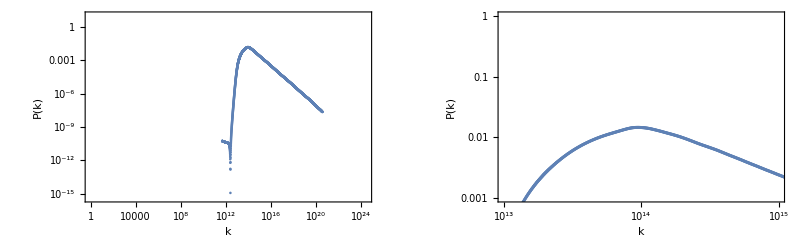

```mathematica
c=ListLogLogPlot[PPlist,Frame->True,FrameLabel->{"k","P(k)"},PlotRange->{{1,3*10^24},{4*10^-16,10}},GridLines->{{0.05},{10^-2,10^-3}}(*,Joined->True*)];

cc=ListLogLogPlot[PPlist,Frame->True,FrameLabel->{"k","P(k)"},GridLines->{{1*10^14},{1.3*10^-2}},PlotRange->{{10^13,10^15},{10^-3,1}}(*,Joined->True*)];

GraphicsRow[{c,cc},ImageSize->Full]
```

```mathematica
W[x_]=Exp[-x^2/2];
```

```mathematica
(*++++++++++++++++We create a list of the Masses+++++++++++++++++++*)
(*eg*)  MMm=M[PPlist[[55,1]]]

MassKList=Table[M[PPlist[[i,1]]],{i,1,Length[PPlist]}];
```

2.62961×10^-11 M_⊙

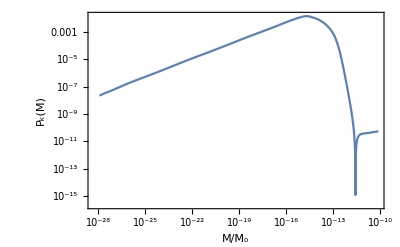

```mathematica
(*Create a list of Subscript[P, k](M)*)
PMList=Table[{M[PPlist[[i,1]]]/Mm,PPlist[[i,2]]},{i,1,Length[PPlist]}]; 

ListLogLogPlot[PMList,Frame->True,FrameLabel->{"M/M_o","P_k(M)"},GridLines->{{10^-16,10^-15,10^-13,1},{1}},Joined->True]
```

The next table does the following computation: It actually does “qqq” repetitions and for each repetition the variance is calculated for different smoothing scale. The each integration runs from k_*to k_end 
σ(k) || k

σ^2=∫ dq/q e^(-(q/k)^2)16/81(q/k)^4 P(q)

```mathematica
SetSystemOptions["CatchMachineUnderflow"->False];

 R=5*10^(13);

(*+++++++++++++++++++++ MANY POINT CALCULATION +++++++++++++++++++++++++++*)
dataaa= Table[{PPlist[[i,1]],1/PPlist[[i,1]] W[PPlist[[i,1]]/R]^2 16/81(PPlist[[i,1]]/R)^4 PPlist[[i,2]]},{i,1,qq}]; (*Makes a list of {k, σ^2=4/25 Int...}*)

σ2kk=Integrate[Interpolation[dataaa][x],{x,PPlist[[1,1]],PPlist[[qq,1]]}]
σ=Sqrt[σ2kk]
```

0.00113305

0.0336608

then we can choose k_limas the lowest values of scales for the MD period.

BEGINNING OF PBH ABUNDANCE CALCULATION

Now we calculate the variance square root of σ^2

for the Radiation Domination period
σ^2=∫ dq/q e^(-(q/k)^2)16/81(q/k)^4 P(q)
for the Matter Domination period
σ^2=∫ dq/q e^(-(q/k)^2)4/25(q/k)^4 P(q)

BE CAREFUL THE FOLLOWING CALCULATION TAKES ABOUT ~ 40 mins if you integrate to large scales with small steps e.g k_final~10^17

```mathematica
(*  Now we create the table sigmak=[k,σ(k)]  *)

sigmak=Table[{Kk (*scale "k"*),datA=Table[{PPlist[[i,1]],(*σ^2=*)1/PPlist[[i,1]] W[PPlist[[i,1]]/Kk]^2 16/81(PPlist[[i,1]]/Kk)^4 PPlist[[i,2]]},{i,1,qq}];

σ2K=Sqrt[Integrate[Interpolation[datA][x],{x,PPlist[[1,1]],PPlist[[qq,1]]}]]},{Kk,(*PPlist[[1,1]]*)10^12,(*PPlist[[Length[PPlist],1]]*)10^16,10^12}];//Timing
```

{372.381,Null}

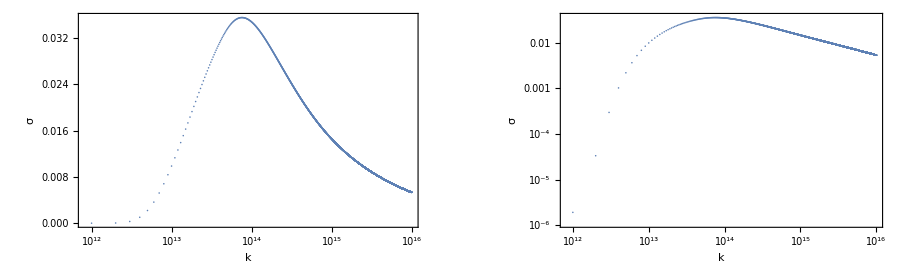

```mathematica
(*Then we plot the σ(k)*)
σk1=ListLogLinearPlot[sigmak,Frame->True,FrameLabel->{"k","σ"}(*,Joined->True*),PlotRange->All];
σk2=ListLogLogPlot[sigmak,Frame->True,FrameLabel->{"k","σ"}(*,Joined->True*),PlotRange->All];

GraphicsRow[{σk1,σk2},ImageSize->900]
```

```mathematica
(* we re-write the mass formula for γ=? *)
Subscript[M, PBH]=M[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(k/10^6)^-2
```

(1.8×10^13)/k^2

Now we go from σ(k) -> σ(Μ) (* We do all the calculation with k as the variable and when it comes to the abundance we map the quantities from k->M *)

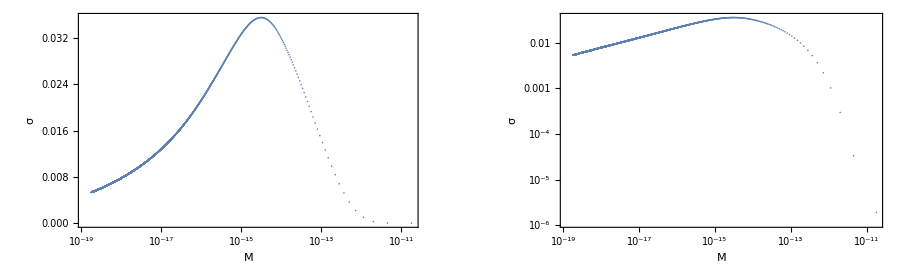

```mathematica
σm=Table[{M[sigmak[[i,1]]] (* M(k) *),sigmak[[i,2]](* σ(k) *)},{i,1,Length[sigmak]}];


(*Plots*)
σm1=ListLogLinearPlot[σm,Frame->True,FrameLabel->{"M","σ"}(*,Joined->True*),PlotRange->All];
σm2=ListLogLogPlot[σm,Frame->True,FrameLabel->{"M","σ"},(*Joined->True,*)PlotRange->All];

GraphicsRow[{σm1,σm2},ImageSize->900]
```

We assume that curvature perturbations are described by Gaussian statistics in order to estimate the PBH formation probability and connect the collapse threshold to the power spectrum:
Radiation Domination ->  β(k)=1/2 Erfc(δ_c/(√2 σ(k))),  
Matter Domination      ->  β(k) = 0.056 σ^5(k)

BE CAREFUL THE FOLLOWING CALCULATION TAKE ABOUT ~ 40 mins because it integrates the for k_final~10^17

```mathematica
N[1/3]
```

0.333333

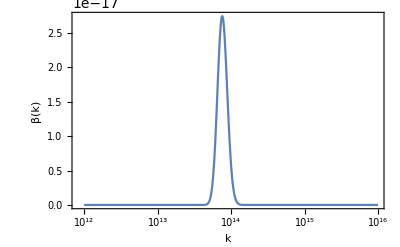

```mathematica
δ=0.298;
ββ=Table[{sigmak[[i,1]](* k *),1/2 Erfc[δ/(√2 sigmak[[i,2]](* σ(k) *))]},{i,1,Length[sigmak]}];
(*PLOT of β(k)*)
βkk=ListLogLinearPlot[ββ,Frame->True,FrameLabel->{"k","β(k)"},Joined->True,PlotRange->Full]
```

Now we go from β(k) -> β(Μ)

{0.054411,Null}

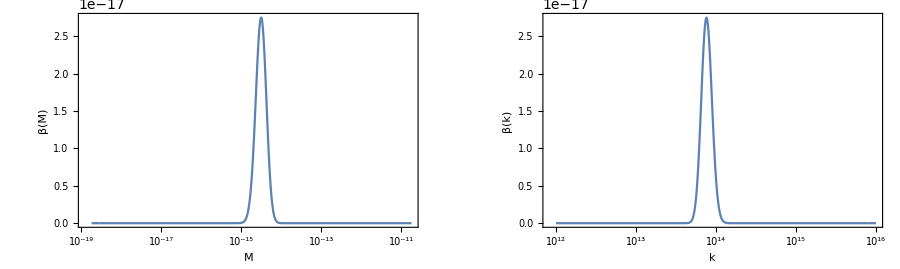

```mathematica
M[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(k/10^6)^-2;

βm=Table[{M[ββ[[i,1]]](* M(k) *),ββ[[i,2]](*β(M)*)},{i,1,Length[ββ]}];//Timing

(*PLOT of β(M)*)
βmm=ListLogLinearPlot[βm,Frame->True,FrameLabel->{"M","β(M)"},Joined->True,PlotRange->All];
GraphicsRow[{βmm,βkk},ImageSize->900]
```

Primordial black hole as Dark Matter fraction Ω_PBH/Ω_DM. We calculate both f(M) and f(k) and compare.

We calculate the f(M) from the standard formula

```mathematica
(*f(m)->Table[M,f(M)]*)

fm=Table[{βm[[i,1]](*M(k)*),1.3*10^8 βm[[i,2]](γ/0.2)^(1/2)(g/106.75)^(-1/4)(βm[[i,1]]/1)^(-1/2)(*f(M)*)},{i,1,Length[βm]}];
```

We calculate the f(k)

```mathematica
3.6(γ/0.2)(g/106.75)^(-1/6)(k/10^6)^-2
```

(1.8×10^13)/k^2

```mathematica
Kk[m_]=Sqrt[(1.8*^13)/m]; (*This is for γ=1*)

ffk=Table[{Kk[fm[[i,1]]](*k*),fm[[i,2]](*f(m)*)},{i,1,Length[fm]}];//Timing
(*we find  f(k) ->  [k,f(k)] *)
```

{0.04585,Null}

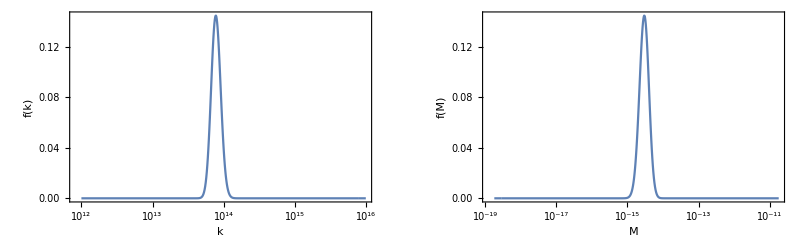

```mathematica
Dfk=ListLogLinearPlot[ffk,Frame->True,FrameLabel->{"k","f(k)"},PlotRange->All,Joined->True];
Dfm=ListLogLinearPlot[fm,Frame->True,FrameLabel->{"M","f(M)"},PlotRange->All,Joined->True];
GraphicsGrid[{{Dfk,Dfm}},ImageSize->800]
```

```mathematica
(*ⅇ^(-3/4 (4(57-Nend)-2*Log[ββ[[Length[ββ],1]]/ββ[[i,1]]]))**)
```

We plot the the PBH DM fraction

```mathematica
Subscript[Massk, i]=mk[ββ[[1,1]]]                     (*Highest Mass Considered*)
Subscript[Massk, f]=mk[ββ[[Length[ββ],1]]](*Lightest Mass Considered*)
```

1.8×10^-11

1.8×10^-19

Finally we want to calculate the integral

(f(M))_(PBH,tot)=∫ dln k  f(M)

```mathematica
(*Relation which connects PBH mass to wavenumber*)
(*1*)   Subscript[M, PBH]=M[k_]=3.6Mm(γ/0.2)(g/106.75)^(-1/6)(k/10^6)^-2
```

(1.8×10^13 M_⊙)/k^2

```mathematica
(*test*)
mk[k_]=(1.8*^13)/k^2;

(*We make the table [M(k),1/(M(k))f(k)]*)
fMoverM=Table[{mk[ββ[[i,1]]](*M(k)*),1/(mk[ββ[[i,1]]](*M(k)*))fm[[i,2]](*f(k)*)},{i,1,Length[ββ]}];

(*  Subscript[f(M), PBH,tot]=∫ dln M  f(M)  *)
Integrate[Interpolation[fMoverM][x],{x,mk[ββ[[Length[ββ],1]]](*Highest Mass Subscript[M, f]*),mk[ββ[[1,1]]](*Lightest Mass Subscript[M, i]*)}]
```

0.111061

OBSERVATIONAL CONSTRAINTS

```mathematica
Femto10={{7.215694633714848*^-17,0.4225706024204134},{9.042559825430532*^-17,0.346392392409924},{1.268560715912728*^-16,0.24870439112267212},{1.992222076446007*^-16,0.1785659140299498},{2.4966116536630553*^-16,0.14637524193450863},{4.38918721965975*^-16,0.12820757007713587},{9.670088830453963*^-16,0.13699056203942026},{2.6698696975354583*^-15,0.16711736630290386},{5.882154451116472*^-15,0.2327589957925409},{8.251944367160743*^-15,0.34639239240992187},{9.237680000320667*^-15,0.4824510294242719},{1.1576470221007345*^-14,0.671951812143415},{1.2959336936453652*^-14,0.8758828910048683},{1.2959336936453652*^-14,1.}};
WD10={{6.584806939333661*^-15,0.10509516438130892},{8.251944367160642*^-15,0.09205105640893374},{1.1576470221007297*^-14,0.11229481712787227},{1.624037400339145*^-14,0.14637524193450951},{2.278326145489651*^-14,0.20386962214216423},{3.196213353299468*^-14,0.30339917008610046},{4.483897013618429*^-14,0.4225706024204134},{6.290359937324404*^-14,0.628870396334644},{7.882949451737491*^-14,0.7671708387550648},{9.87874981365207*^-14,1.}};
Kep10={{3.4180218482566466*^-13,0.9358861528011254},{4.2833945470856333*^-13,0.7179845648236842},{6.009079462107862*^-13,0.5155018353250516},{7.530454556376062*^-13,0.3701223609016646},{1.0564308124696155*^-12,0.26574214222349435},{1.4820434187339352*^-12,0.19079875633964766},{1.857266272767386*^-12,0.14637524193450951},{2.916759776676187*^-12,0.10509516438130956},{4.5806504536151906*^-12,0.07545670586338749},{1.0091913279368402*^-11,0.0474524885224151},{2.2234116021210858*^-11,0.03889807036015874},{3.9088857787532214*^-11,0.031885785653351754},{7.692946554041374*^-11,0.027928214120019598},{1.6948804601522992*^-10,0.026137628867391},{3.3356371952110457*^-10,0.026137628867391},{1.3669782022938304*^-9,0.04156282283238898},{3.56712132477627*^-9,0.0507032702432767},{9.30838145357531*^-9,0.057888184326909425},{2.5700038553663365*^-8,0.057888184326909425},{5.662133860384365*^-8,0.06185387416369976},{8.892146773072757*^-8,0.06185387416369976},{1.5632906669503587*^-7,0.0806259454075109},{2.455083260527815*^-7,0.10509516438131074},{4.3161779103685803*^-7,0.16711736630290694},{6.778378686209039*^-7,0.24870439112267517},{9.509237522236146*^-7,0.3701223609016669},{1.4933863775165935*^-6,0.5508168208089749},{1.8714810349761835*^-6,0.819726669166882},{2.345301468532118*^-6,1.}};
HSC10={{3.785695644098578*^-14,1.},{5.94527825296265*^-14,0.5885510958361514},{7.450500195788969*^-14,0.39547797538609625},{9.336813317322828*^-14,0.28394708205493774},{1.309840887406306*^-13,0.19079875633965115},{2.0570508764690408*^-13,0.11229481712787504},{2.885791172963822*^-13,0.07545670586338933},{3.6164140321706334*^-13,0.05788818432691043},{4.5320155438165574*^-13,0.04156282283238996},{7.117342752247852*^-13,0.026137628867391613},{9.984762712651405*^-13,0.0175632270825759},{1.5680656396416117*^-12,0.013473995652185397},{2.75674979526928*^-12,0.00905387579529851},{4.329361403424796*^-12,0.006945869487863323},{9.538282888170431*^-12,0.004987027081565644},{2.3524650438682616*^-11,0.00382590174905893},{5.182860699778358*^-11,0.0033510418846663587},{1.1418679781586332*^-10,0.0033510418846663587},{2.0074697355990864*^-10,0.0033510418846663587},{4.4227802771183914*^-10,0.003580608468921833},{1.3669782022938304*^-9,0.004987027081565674},{3.56712132477627*^-9,0.006500543072855155},{9.30838145357531*^-9,0.007421703448730786},{2.2957635290609317*^-8,0.007930134906385295},{5.057938098493036*^-8,0.007421703448730786},{7.943282347242757*^-8,0.007421703448730786},{1.3964748305774016*^-7,0.009053875795298733},{1.9590836500183497*^-7,0.01180164226522358},{2.748355117995443*^-7,0.016437181025084867},{4.831766743255008*^-7,0.022893501936384203},{6.778378686209095*^-7,0.03188578565335364},{1.0645163051151815*^-6,0.0507032702432794},{1.4933863775166058*^-6,0.07545670586339243},{1.8714810349761951*^-6,0.09835710907083131},{2.9390834721277242*^-6,0.17856591402996258},{3.683198843320025*^-6,0.2657421422235118},{5.167078185527541*^-6,0.42257060242044103},{6.475275907186635*^-6,0.5885510958361833},{7.248779691537976*^-6,0.7671708387551149},{0.00001016915268741752,1.0685060324987845}};
EROS10={{4.036084637484883*^-8,1.},{5.6621338603844113*^-8,0.6288703963346929},{6.33850379910012*^-8,0.4225706024204488},{9.954357755055165*^-8,0.28394708205495806},{1.5632906669503683*^-7,0.2178359211021547},{2.1931058969265144*^-7,0.1564028290154968},{3.8556066018625575*^-7,0.13699056203943538},{6.778378686209095*^-7,0.11229481712788503},{1.334029897714027*^-6,0.1050951643813217},{2.3453014685321375*^-6,0.10509516438132235},{5.167078185527498*^-6,0.10509516438132299},{9.084021338130308*^-6,0.11229481712788732},{0.000015970233216663105,0.11998768951948734},{0.000025080589979751875,0.11998768951948807},{0.00004936026509313825,0.11229481712788904},{0.00008677819170953016,0.09835710907083986},{0.00017078523872618873,0.0861493090438496},{0.0003002502956451766,0.07061888615354289},{0.0008289780787685713,0.050703270243284686},{0.0018263726879284537,0.041562822832395915},{0.004504456363687841,0.0364041654207626},{0.007919093974429553,0.0340701543215731},{0.01953117974416327,0.0364041654207629},{0.043030345628379034,0.04156282283239664},{0.07564982836337929,0.04745248852242441},{0.13299675956203397,0.05788818432692044},{0.18657821212264303,0.05788818432692079},{0.3280152533591409,0.05070327024328681},{0.4601653432928822,0.05417675012236442},{0.6455557813221896,0.07545670586340461},{1.0138186237322362,0.11229481712789811},{1.9952623149688258,0.16711736630294383},{3.133476846886012,0.21783592110218522},{6.903555929862501,0.3241838434921761},{9.684845908457087,0.395477975386186},{15.209649474226227,0.5508168208091044},{19.060419304871775,0.717984564823859}};
CMB10={{9451.411862277744,0.00006719518121434185},{6737.1593749802,0.00011801642265222953},{4802.3847765052315,0.00021425711451386346},{3832.1606635555395,0.0003188578565335182},{3057.950588038721,0.0005417675012235306},{2179.7696230609854,0.0009835710907082538},{1739.39153021936,0.001671173663029059},{1387.9828691025853,0.0024870439112267364},{1107.569176606994,0.004225706024204134},{883.8073641089258,0.006719518121434185},{705.2520721514585,0.013034906300958566},{502.71807840509746,0.027018092005137904},{320.10909475589403,0.056001729413614164},{255.437566554716,0.10863536378740991},{203.83160452579833,0.24059963492679937},{129.7911358477477,0.49870270815654555},{103.56947816994445,0.7930134906384897},{103.56947816994445,0.9674120904770179}};
UFD10={{10580.429829653898,0.003033991700861001},{5376.053428124171,0.00515501835325051},{3423.2379342630365,0.007671708387550639},{1947.1704651060807,0.012199188310127286},{989.3825319588277,0.020727492305143345},{502.718078405083,0.03521782977176571},{255.43756655470867,0.06831756428094825},{129.79113584774402,0.11607754154954239},{73.82643894710947,0.18458102373096014},{41.993184295767115,0.2935120253819988},{21.337280812389622,0.46672895892814903},{15.209649474224921,0.6500543072855162},{10.84174872903511,0.9053875795298677}};
Radio10={{145.29532998440808,0.019398573030676033},{129.79113584774348,0.028868994294096353},{92.51777199086337,0.04590611111980882},{65.94855710481247,0.07299772955981325},{47.009478185836564,0.10863536378741546},{33.50931599295583,0.17274682417966275},{23.886124706103942,0.24059963492681166},{19.060419304869903,0.3580608468921866},{15.20964947422461,0.498702708156572},{10.841748729034888,0.7421703448730809}};
EG10={{6.675799908777158*^-19,1.785659140299602*^-7},{7.473257278474755*^-19,2.6574214222350794*^-7},{8.365974881429097*^-19,4.824510294243021*^-7},{1.173644110713773*^-18,1.3034906300959286*^-6},{1.6464793621013692*^-18,3.7630463562645612*^-6},{2.309809477233271*^-18,0.000013252632599818597},{3.2403806229963843*^-18,0.00003825901749058781},{4.5458582993033295*^-18,0.00011801642265222953},{5.696775946880334*^-18,0.0002792821412001957},{7.139082226546229*^-18,0.0005788818432690925},{8.94655073547327*^-18,0.0011998768951947125},{1.1211633025428775*^-17,0.0021783592110213466},{1.40501874759933*^-17,0.00451519237842824},{1.971069722218343*^-17,0.01000000000000001},{2.2065237648274084*^-17,0.0193985730306751},{2.765170113554801*^-17,0.0376304635626435},{3.465254206085899*^-17,0.07799851439336582},{4.342585164628078*^-17,0.13252632599817826},{4.8613284748520736*^-17,0.24059963492679937},{6.092116670171166*^-17,0.46672895892812805},{6.819850185565801*^-17,0.7421703448730415},{7.634515074422419*^-17,0.9674120904770179}};


Ticks2={{{(*{10^-7, "",0.01 }*){10^-7, Superscript[10,-7]},{10^-6, Superscript[10,-6]},{10^-5, Superscript[10,-5]},{10^-4, Superscript[10,-4]},{10^-3, Superscript[10,-3]},{10^-2, Superscript[10,-2]},{10^-1, Superscript[10,-1] },{0, 1},{10^0, Superscript[1,""]}}, None},  {{{10^-18, "",0.01 },{10^-17, "",0.01 },{10^-16, "",0.01 },{10^-15, Superscript[10,-15]},{10^-14, "",0.01 },{10^-13, "",0.01 },{10^-12, "",0.01 },{10^-11, "",0.01 },{10^-10, Superscript[10,-10]},{10^-9, "",0.01 },{10^-8, "",0.01 },{10^-7, "",0.01 },{10^-6, "",0.01 },{10^-5, Superscript[10,-5]},{10^-4, "",0.01 },{10^-3, "",0.01 },{10^-2, "",0.01 },{10^-1, "",0.01 },{10^0, Superscript[10,0]},{10^1, "",0.01 },{10^2, "",0.01 },{10^3, "",0.01 },{10^4, Superscript[10,4]}}, { {10^-17.3,  Superscript[10,16]},{10^-16.3,"",0.01},{10^-15.3,  "",0.01},{10^-14.3,  "",0.01},{10^-13.3,"",0.01},{10^-12.3 ,Superscript[10,21]} ,{10^-11.3,  "",0.01},{10^-10.3, "",0.01},{10^-9.3,"",0.01},{10^-8.3,  "",0.01}, {10^-7.3,Superscript[10,26]},{10^-6.3,"",0.01},{10^-5.3,"",0.01},{10^-4.3, "",0.01}, {10^-3.3, "",0.01},{10^-2.3, Superscript[10,31]}, {10^-1.3, "",0.01},{10^-0.3, "",0.01},{10^0.7, "",0.01},{10^1.7, "",0.01},{10^2.7,Superscript[10,36]},{10^3.7, "",0.01}}}};


ticksA={{     {{10^-7, Superscript[10,-7] }, {10^-6, Superscript[10,-6]},{10^-5,  Superscript[10,-5] },{10^-4, Superscript[10,-4]}, {10^-3, "",0.01 },{10^-2, Superscript[10,-2]}, {10^-1, "",0.01 },{0,1}}, None},  {{ {10^-19," ", 0.01},{-18," ", 0.01} , {10^-17, Superscript[10,-17]},{10^-16," ", 0.01}, {10^-15, Superscript[10,-15]},{-14," ", 0.01}, {10^-13," ", 0.01}, {-12," ", 0.01}, {10^-11," ", 0.01},  {-10, Superscript[10,-10]},{10^-9," ", 0.01},{-8," ", 0.01} , {10^-7," ", 0.01}, {10^-6," ", 0.01} , {10^-5, Superscript[10,-5]},{-4," ", 0.01}, {10^-3," ", 0.01}, {10^-2," ", 0.01}, {10^-1," ", 0.01},{0, 1}, {1," ", 0.01},  {2," ", 0.01}, {3," ", 0.01},{4, Superscript[10,4]}}, {{10^-15.3," ", 0.01}, {10^-17.3,  Superscript[10,16]},{-16.3," ", 0.01},{10^-15.3," ", 0.01},{10^-14.3," ", 0.01}, {10^-13.3," ", 0.01},{-12.3 ,Superscript[10,21]} , 
{10^-11.3," ",0.01},{10^-10.3," ", 0.01},{-9.3," ", 0.01}, {-8.3," ", 0.01},{10^-7.3,Superscript[10,26]},{-6.3," ", 0.01},{-5.3," ", 0.01},{-4.3," ", 0.01}, {10^-3.3," ", 0.01}, {-2.3, Superscript[10,31]}, {-1.3," ", 0.01},{-0.3," ", 0.01},{1.3," ", 0.01}, {2.3," ", 0.01},{3.3, Superscript[10,36]}}}} ;


APlot=Show[ ListLogLogPlot[{Kep10, EROS10, EG10, Femto10, WD10, HSC10, CMB10, UFD10, Radio10}, Filling->{1->Top, 2->Top, 3->Top, 4->Top, 5->Top, 7->Top, 8->Top, 9->Top}, PlotStyle->{{Thick, Blue},{Thick, Blue},{Thick, Green},{Thick, Blue},{Thick, Orange},{Dashed, Thick, Blue}, {Red, Thick}, {Thick, Orange},{Thick, Dashed, Orange}, {Thick, Dashed, Black}}, PlotRange->{{10^-18.2,10^4},{10^-7,1}}, PlotRangePadding->.01, Frame->True, 
FrameStyle->{20,20},  
FrameTicks->Ticks2,
FrameLabel->{{"Ω_PBH/Ω_cr", " "},{"M_PBH/M_⊙", "M_PBH[g]" }}, 
 Axes->False,Joined->True],ImageSize->500];
```

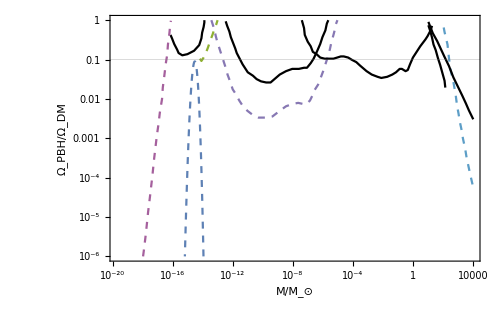

```mathematica
(*fmass=Table[{mk[ββ[[i,1]]],fk[[i,2]]},{i,1,Length[ββ]}];(*[M(k),f(k)]*)*)

PBH=ListLogLogPlot[{fm,Femto10,WD10,Kep10,HSC10,EROS10,CMB10,UFD10,EG10,Radio10},


Frame->True,FrameLabel->{"M/M_⊙","Ω_PBH/Ω_DM"},PlotRange->{{2*10^-20,10^4},{10^-6,1}},BaseStyle->{FontFamily->"Arial",20},GridLines->{{ },{0.1}},PlotStyle->{Dashed,Black},Joined->True,ImageSize->500]
```

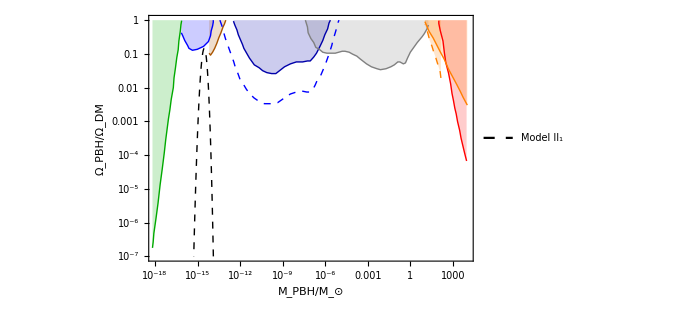

```mathematica
PBH2=ListLogLogPlot[{fm,Kep10, EROS10, EG10, Femto10, WD10, HSC10, CMB10, UFD10, Radio10},Filling->{2->Top, 3->Top, 4->Top, 5->Top, 6->Top, 8->Top, 9->Top, 10->Top},PlotStyle->{ {Thick, Dashed, Black},{Thick, Darker[Blue]},{Thick, Gray},{Thick,Darker[Green]},{Thick,Blue},{Thick, Darker[Orange]},{Dashed, Thick,Blue}, {Red, Thick}, {Thick, Orange},{Thick, Dashed, Orange}},Frame->True,FrameLabel->{{"Ω_PBH/Ω_DM", " "},{"M_PBH/M_⊙", "M_PBH[g]" }},PlotRange->{{1*10^-18,10^4},{10^-7,1}},BaseStyle->{FontFamily->"Arial",20}(*,GridLines->{{0},{0.1}}*),PlotStyle->{Dashed,Black},Joined->True,ImageSize->500,FrameTicks->Ticks2,FrameStyle->Directive[FontSize->16],PlotLegends->Placed[LineLegend[{"Model II_1"},LabelStyle->{GrayLevel[0.1],16},LegendLayout->{"Row",1},LegendMarkerSize->15 ],{0.85,.15}]]
```